# CellFIT : A Cellular Force - Inference Toolkit Using Curvilinear Cell Boundaries

Starting from a user-provided segmentation of a field of closely packed cells, this notebook applies the Cellular Force Inference Toolkit (CellFIT) to provide linear least-squares estimates for the tensions along each cell-cell interface and the pressures inside each cell. The basic theory assumes that forces in the cell sheet are in near-equilibrium and that one can thus setup two systems of equations: one that results from force balance of the tensions meeting at each triple and quad junction; and one that results from how those tensions and the curvature of cell-cell interfaces balance pressure differences.  We hope you find it useful!

For more information, see the original 2014 paper describing CellFIT and the follow-up 2015 book chapter that provides additional practical details:

G.W. Brodland, J.H. Veldhuis, S. Kim, M. Perrone, D. Mashburn and M.S. Hutson (2014) “CellFIT: a cellular force-inference toolkit using curvilinear cell boundaries” PLoS ONE 9: e99116 (15pp), https://doi.org/10.1371/journal.pone.0099116.

J.H. Veldhuis, D. Mashburn, M.S. Hutson, G.W. Brodland “Practical Aspects of the Cellular Force Inference Toolkit (CellFIT)”, in Methods in Cell Biology Volume 125: Biophysical Methods in Cell Biology, edited by E. Paluch, Chapter 18, pp. 331-351 (Elsevier, 2015), https://doi.org/10.1016/bs.mcb.2014.10.010. 

If you have questions or suggestions for improvement, please email shane.hutson@vanderbilt.edu.

### Using This Notebook

There are multiple ways to use this Mathematica notebook, depending on how much you want to change parameters and evaluate intermediate results. 

(1) You can step through and evaluate one cell at a time, inspecting all of the intermediate outputs and annotations. One of the earliest steps will provide a file dialog box that will let you choose the segmented image to analyze. You will also see several cells with a light blue background that define CellFIT parameters. The parameters in these cells can be changed by the user to alter how the CellFIT process proceeds. This step-by-step process is certainly the best way to see all the nuances of how CellFIT works and it is available to make the methods as transparent as possible. 

(2) You can evaluate the notebook one section at a time. The parameters applicable to each section are defined at the start of each section (cells with light blue backgrounds), and you can change these to alter how the CellFIT process proceeds. Each section ends with an output visualization that will help you evaluate the validity of that step in the process. Sections are organized following the steps in the book chapter Practical Aspects of the Cellular Force Inference Toolkit (CellFIT).

-Graphics-

(3) You can also evaluate the entire notebook by using the Mathematica menus to select Evaluation > Evaluate Notebook. This method is useful once you have all the parameters set and you want to apply CellFIT sequentially to multiple segmented images using the exact same parameters. On most desktop computers, it takes a few minutes to evaluate the entire notebook. You can see the evaluation progress by following which notebook cell brackets are highlighted.

## 1 - Image Segmentation (Import, Interpretation and QA Checks)

This notebook assumes that the user has already segmented their images using any one of many available segmentation routines. When this section is evaluated, it will pop-up a file dialog box that prompts the user to select the segmented image. This can either be a grayscale segment-map image, i.e., one in which the pixels corresponding to each cell have a unique gray level, or as an outline image, i.e., a binary image in which only the cell borders are outlined. In either case, the image should not be in a compressed format. Uncompressed .tif files work best. After loading this image, the rest of this section interprets the image to extract the underlying segmentation. It also conducts a few quality-assurance checks on the segmentation to eliminate cells that would be problematic in later steps.

```mathematica
(* Set the working directory to the notebook file's directory. Then provide a file dialog box that prompts the user to choose the filename of the segmentation. *)
startTime=AbsoluteTime[];
workingDirectory=NotebookDirectory[];SetDirectory[workingDirectory];
Print["Select Segmentation ..."];
segmentFilename =SystemDialogInput["FileOpen",workingDirectory,WindowTitle->"Select Segmentation ..."]
If[!StringContainsQ[Last[StringSplit[segmentFilename,"."]],"tif"],Print["WARNING! File selected is not in '.tif' format. CellFIT may fail if the selected image has lossy compression."]]
```

Select Segmentation ...

/Users/hutsonms/Library/CloudStorage/Box-Box/Research Sync/Mathematica Notebook Development/CreateMesh_UniformPressure_Outlines_2024.tif

```mathematica
(* Import the selected image (inputImage)*)
inputImage=Import[segmentFilename];
{w,h} = ImageDimensions[inputImage];
type=ImageType[inputImage];
Print["Image size = ",w," x ",h," pixels. Image type = ",type]
ImageAdjust[inputImage]
```

Image size = 512 x 512 pixels. Image type = Byte

-Graphics-

```mathematica
(* Determine whether the selected image is 
a segment map (= different gray level for pixels of each cell) or 
a set of cell outlines (= binary image with cell edges one color and everything else either black or white) *)
imageHistogramData=ImageLevels[inputImage,All];
outlineImageQ=Length[imageHistogramData]==2
Print["Input image appears to be in ",If[outlineImageQ,"an outline representation.","a segment-map representation."]]
(* if it is an outline image, then scale it up by a factor of 2 to allow for better processing of outline-type images *)
If[outlineImageQ,
inputImage=ImageResize[Import[segmentFilename],Scaled[2],Resampling->"NearestLeft"];
{w,h} = ImageDimensions[inputImage];
Print["New image size = ",w," x ",h," pixels. Image type = ",type]
]
```

True

Input image appears to be in an outline representation.

New image size = 1024 x 1024 pixels. Image type = Byte

```mathematica
imageHistogramData
```

{{0.,242762},{0.996094,19382}}

```mathematica
(* If the image is in an outline representation, then process to convert to a segment map. *)
timeReq=AbsoluteTiming[
segmentImage=If[outlineImageQ,
(morphCompDataRaw=MorphologicalComponents[ColorNegate[Binarize[inputImage]],CornerNeighbors->False];
(* find all small components, which are isolated bits of cells, and reassign to an adjacent parent cell. *)
(* This is sometimes ambiguous, hence the RandomChoice when a small component is corner-connected to more than one larger cell. *) 
morphCompData=morphCompDataRaw;
labels = ComponentMeasurements[morphCompData,"Label"][[All,2]];
smallAreaList=Select[ComponentMeasurements[morphCompDataRaw,"Area"],#[[2]]<9&];
nSmallArea=Length[smallAreaList];
Print["Outline representation contains ",Length[labels]," morphogical components",If[nSmallArea>0,", but "<>ToString[nSmallArea]<>" of these have very small areas and are likely isolated fragments of larger cells. Will attempt to join these with appropriate larger cell.","."]];
(* Print[smallAreaList]; *)
smallAreaBooleanList=MemberQ[smallAreaList[[All,1]],#]&/@labels;
(* Print[smallAreaBooleanList]; *) 
smallAreaNeighborsList=Pick[ComponentMeasurements[morphCompDataRaw,"ExteriorNeighbors"],smallAreaBooleanList];
(* Print[smallAreaNeighborsList]; *) 
Do[
smallComponent=smallAreaList[[i]];
neighbors=smallAreaNeighborsList[[i]];
pts=Position[morphCompDataRaw,smallComponent[[1]]];
newLabel=If[Length[neighbors[[2]]]>0,RandomChoice[neighbors[[2]]],0]; (* reassign to one of the neigbors or to border (0) if no neighbors *)
Do[ morphCompData[[site[[1]],site[[2]]]]=newLabel;,{site,pts}];
,{i,1,Length[smallAreaList]}];

morphCompDataUpdated=morphCompData;
(* morphCompImage=Image[morphCompData]//ImageAdjust; *)
labels = ComponentMeasurements[morphCompData,"Label"][[All,2]];
If[nSmallArea>0,Print["After joining small fragments to larger cells, there are now ",Length[labels]," morphological components."]];
count=1;
listOfBorderPixels=Position[morphCompData,0];
areaOfBorder=Length[listOfBorderPixels];
Print["Attempting to reassign pixels in the outlines to adjacent cells."];
Print["\tRound #",count," of using 3x3 Commonest filter to reassign all border pixels (",areaOfBorder," left)."];
Do[
site3x3 =morphCompData[[#[[1]],#[[2]]]]&/@Flatten[Table[site+{i,j},{i,{-1,0,1}},{j,{-1,0,1}}],1];
mostCommonLabel=Commonest[Select[site3x3,Positive]];
newLabel=Switch[Length[mostCommonLabel],0,0,1,mostCommonLabel[[1]],_,RandomChoice[mostCommonLabel]];
morphCompDataUpdated[[site[[1]],site[[2]]]]=newLabel;
,{site,listOfBorderPixels}];
morphCompData=morphCompDataUpdated;
listOfBorderPixels=Position[morphCompData,0];
areaOfBorder=Length[listOfBorderPixels];
While[(areaOfBorder>0)&&(count<5),
count+=1;
Print["\tRound #",count," of using 3x3 Commonest filter to reassign all border pixels (",areaOfBorder," left)."];
listOfBorderPixels=Position[morphCompData,0];
Do[
site3x3 =morphCompData[[#[[1]],#[[2]]]]&/@Flatten[Table[site+{i,j},{i,{-1,0,1}},{j,{-1,0,1}}],1];
mostCommonLabel=Commonest[Select[site3x3,Positive]];
newLabel=Switch[Length[mostCommonLabel],0,0,1,mostCommonLabel[[1]],_,RandomChoice[mostCommonLabel]];
morphCompDataUpdated[[site[[1]],site[[2]]]]=newLabel;
,{site,listOfBorderPixels}];
morphCompData=morphCompDataUpdated;
listOfBorderPixels=Position[morphCompData,0];
areaOfBorder=Length[listOfBorderPixels];
];
filteredImage=Image[morphCompData]//ImageAdjust
)
,inputImage
]//ImageAdjust][[1]];
If[outlineImageQ,Print["Conversion of outline representation to segment map took ",timeReq, " seconds."]]
segmentImage
type=ImageType[segmentImage]
```

Outline representation contains 101 morphogical components.

Attempting to reassign pixels in the outlines to adjacent cells.

Round #1 of using 3x3 Commonest filter to reassign all border pixels (77528 left).

Round #2 of using 3x3 Commonest filter to reassign all border pixels (33484 left).

Conversion of outline representation to segment map took 4.86663 seconds.

-Graphics-

Real32

Segmented image contains 101 cells.

Excluding 1 cell(s) that lies on the boundary of the image. Excluded cellIDs = {6554}

Excluding 0 cell(s) that have two or more separated regions. Excluded cellIDs = {6554}

Excluding 0 cell(s) that have areas less than 9. Excluded cellIDs = {6554}

Excluding 6 cell(s) that are further than 512 pixels from the image center. Excluded cellIDs = {0,5898,6554,7209,58982,61603,62258}

Excluding 0 cell(s) that have contact with two or fewer cells. Excluded cellIDs = {0,5898,6554,7209,58982,61603,62258}

... and 0 cell(s) that surround those cells. Excluded cellIDs = {0,5898,6554,7209,58982,61603,62258}

Force-inference will be applied to 94 cells.

Colorized graphic of the cell regions to be included in CellFIT analysis.

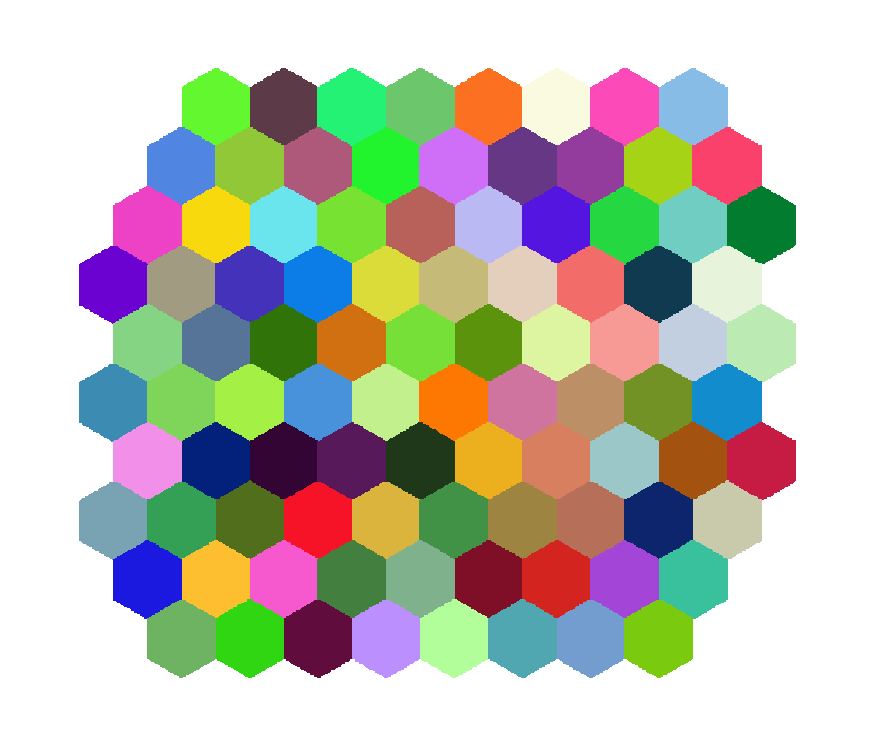

... and the cell regions that have been excluded.

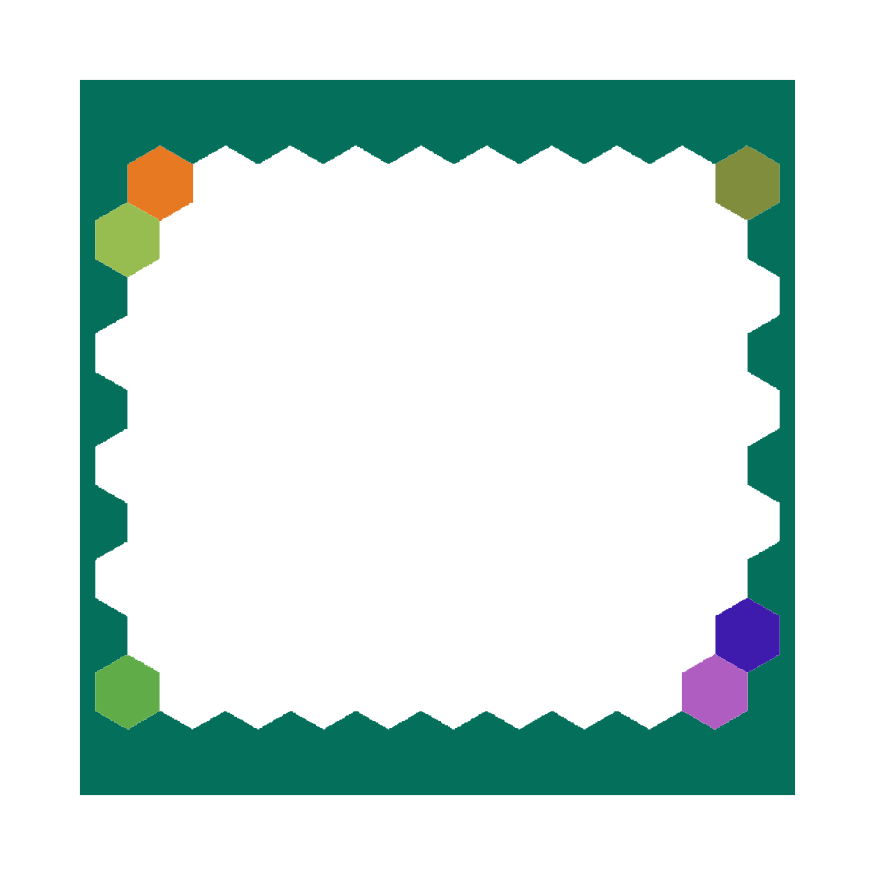

```mathematica
(* Get a list of cell IDs and exclude cells from further analysis based on a few quality-assurance criteria. *)
testAllExclusionCriteria=False; (* only set this True during initial testing to turn good segmentations into bad ones to test exclusion criteria *)
pixelArray=ImageData[segmentImage,"Bit16"];
cellIDs=Sort[DeleteDuplicates[Flatten[pixelArray]]];
nCellsAll=Length[cellIDs];
Print["Segmented image contains ",nCellsAll," cells."];
(* first criterion for exclusion: being on the boundary of the image *)
excludedCellIDs=DeleteDuplicates[Join[pixelArray[[All,1]],pixelArray[[All,-1]],pixelArray[[1]],pixelArray[[-1]]]];
includedCellIDs=Complement[cellIDs,excludedCellIDs];
nCells=Length[includedCellIDs];
Print["\tExcluding ",Length[excludedCellIDs]," cell(s) that lies on the boundary of the image. Excluded cellIDs = ",excludedCellIDs];
(* second criterion for exclusion: cells with two or more separated regions *)
cellRegionList=Table[ImageMesh[Binarize[segmentImage,{ci-1,ci+1}/(2^16 -1)],Method->"Exact"],{ci,cellIDs}];
(*  Just to test exclusion criteria; make one of the regions disjointed on purpose by joining with another randomly selected region *)
If[testAllExclusionCriteria,
i1=RandomInteger[nCellsAll]; i2=RandomInteger[nCellsAll];
testRegion=RegionUnion[cellRegionList[[i1]],cellRegionList[[i2]]];
cellRegionList[[i1]]=testRegion;
]
additionsToExcludedCellIDs=cellIDs[[Flatten[Position[Length[ConnectedMeshComponents[#]]&/@cellRegionList,x_/;x>1]]]];
excludedCellIDs=Union[excludedCellIDs,additionsToExcludedCellIDs];
includedCellIDs=Complement[cellIDs,excludedCellIDs];
Print["\tExcluding ",Length[additionsToExcludedCellIDs]," cell(s) that have two or more separated regions. Excluded cellIDs = ",excludedCellIDs];
(* third criterion for exlusion: cell with area less than a given cutoff *)
areaMin=9;
additionsToExcludedCellIDs=cellIDs[[Flatten[Position[RegionMeasure[#]&/@cellRegionList,area_/;area<=areaMin]]]];
excludedCellIDs=Union[excludedCellIDs,additionsToExcludedCellIDs];
includedCellIDs=Complement[cellIDs,excludedCellIDs];
Print["\tExcluding ",Length[additionsToExcludedCellIDs]," cell(s) that have areas less than ",areaMin,". Excluded cellIDs = ",excludedCellIDs];
(* fourth criterion for exclusion: cell centroid is beyond a designated difference from center of image *)
(* rMax=300; *)
rMax=Max[w,h]/2;
additionsToExcludedCellIDs=cellIDs[[Flatten[Position[EuclideanDistance[{w/2,h/2},RegionCentroid[#]]&/@cellRegionList,r_/;r>rMax]]]];
excludedCellIDs=Union[excludedCellIDs,additionsToExcludedCellIDs];
includedCellIDs=Complement[cellIDs,excludedCellIDs];
Print["\tExcluding ",Length[additionsToExcludedCellIDs]," cell(s) that are further than ",rMax," pixels from the image center. Excluded cellIDs = ",excludedCellIDs];
(* fifth criterion for exclusion: making contact with less than two currently included cells *)
neighborPairListBuild={};
Do[
valueSet=Sort[DeleteDuplicates[Flatten[pixelArray[[i;;i+1,j;;j+1]]]]];
If[Length[valueSet]>1 ,AppendTo[neighborPairListBuild,Subsets[valueSet,{2}]]]
,{i,1,h-1},{j,1,w-1}];
neighborPairList=DeleteDuplicates[Flatten[neighborPairListBuild,1]];
numberOfNeighbors=Table[Length[Complement[DeleteDuplicates[Flatten[Select[neighborPairList,MemberQ[#,cellIDs[[i]]]&]]],{cellIDs[[i]]}]],{i,nCellsAll}];
additionsToExcludedCellIDs=cellIDs[[Flatten[Position[numberOfNeighbors,n_/;n<=2]]]];
excludedCellIDs=Union[excludedCellIDs,additionsToExcludedCellIDs];
includedCellIDs=Complement[cellIDs,excludedCellIDs];
Print["\tExcluding ",Length[additionsToExcludedCellIDs]," cell(s) that have contact with two or fewer cells. Excluded cellIDs = ",excludedCellIDs];
additionsToExcludedCellIDsNeighbors=Complement[DeleteDuplicates[Flatten[Select[neighborPairList,ContainsAny[#,additionsToExcludedCellIDs]&]]],additionsToExcludedCellIDs];
excludedCellIDs=Union[excludedCellIDs,additionsToExcludedCellIDsNeighbors];
includedCellIDs=Complement[cellIDs,excludedCellIDs];
Print["\t... and ",Length[additionsToExcludedCellIDsNeighbors]," cell(s) that surround those cells. Excluded cellIDs = ",excludedCellIDs];
nCells=Length[includedCellIDs];
(* remake cellRegionList so that it only has entries for includedCellIDs *)
cellRegionList=Table[ImageMesh[Binarize[segmentImage,{ci-1,ci+1}/(2^16 -1)],Method->"Exact"],{ci,includedCellIDs}];
centroidList=Table[ RegionCentroid[cellRegion],{cellRegion,cellRegionList}];
cellRegionBoundaryList=RegionBoundary/@cellRegionList;
(* and filter neighborPairList to remove pairs with excludedCellIDs *)
neighborPairListOriginal=neighborPairList;
neighborPairList=Select[neighborPairListOriginal,!(MemberQ[excludedCellIDs,#[[1]]]||MemberQ[excludedCellIDs,#[[2]]])&];
Print["Force-inference will be applied to ",Length[includedCellIDs]," cells.\n"]
(* show a color-coded map of the included and excluded cells *)
Print["Colorized graphic of the cell regions to be included in CellFIT analysis."]
Graphics[{{RandomColor[],#}&/@cellRegionList}]
excludedCellRegionList=Table[ImageMesh[Binarize[segmentImage,{ci-1,ci+1}/(2^16 -1)],Method->"Exact"],{ci,excludedCellIDs}];
Print["... and the cell regions that have been excluded."]
Graphics[{{RandomColor[],#}&/@excludedCellRegionList}]
```

## 2 - Mesh Generation

This section continues interpretation of the segment map to generate a reduced ‘mesh’ that provides a smooth approximation of the segmentation as a set of connected nodes. There will be nodes at each triple- and quad-junction plus a few intermediate nodes along each cell-cell interface. The user is able to specify the desired level of boundary smoothing and a target number of intermediate nodes to be placed along the median-length cell-cell interface.

### Parameter Choices

```mathematica
targetNumberOfIntermediateNodes=4;   (* determines target spacing of nodes along edges based on putting this many intermediate nodes along the median-length cell-cell interface *)
smoothingWindow=3; (* width of smoothing window to apply to boundaries between triple- and quad-junctions; only choices are 3, 5 and 7 right now *)
verbose=True;   (* If verbose = True then lots of extra information is output. *)
```

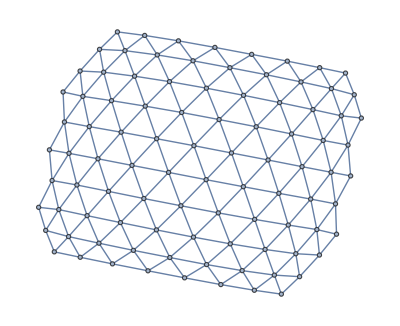

```mathematica
(* A useful graphic for detecting if anything is wrong with the list of neighboring cell pairs. *)
cellConnectionGraph=Graph[#[[1]]<->#[[2]]&/@neighborPairList]
```

```mathematica
(* Two functions that convert from index coordinates (row, col) to image coordinates (x,y). *)
(* These conversions ensure that graphics elements display in same orientation as the original image. *)
r=.; c=.; x=.;y=.;
ConvertToIndexCoord[pt_]:=({h-y+1/2,x+1/2})/.{x-> pt[[1]],y-> pt[[2]]}
ConvertToImageCoord[pt_]:=({c-1/2, h-r+1/2})/.{r-> pt[[1]],c-> pt[[2]]}
```

Finding all boundary locations took 4.60931 s.

Graphical check: boundary points in gray, triple-junctions in blue, and quad-junctions in red.

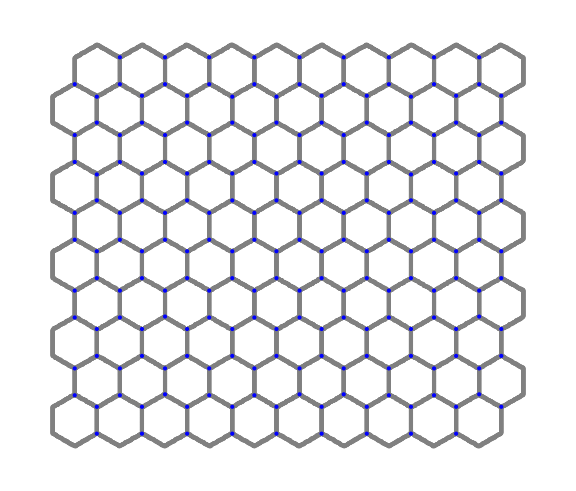

```mathematica
(* Gather a list of coordinates for all cell-cell boundaries and triple- and quad-junctions. 
Note that these are placed at half-pixel locations, i.e., they lie between pixels belonging to different cells. *) 
cellBoundaryPixels={};
timeReq=AbsoluteTiming[
Monitor[
Do[
valueSet=Sort[DeleteDuplicates[Flatten[pixelArray[[i;;i+1,j;;j+1]]]]];
If[Length[valueSet]>=2 ,
AppendTo[cellBoundaryPixels,{valueSet,ConvertToImageCoord[{i+0.5,j+0.5}]}]];
,{j,1,w-1},{i,1,h-1}]
,"Processing image row "<>ToString[j]<>" of "<>ToString[w]]][[1]];
Print["Finding all boundary locations took ",timeReq," s."]
edgePixels=Select[cellBoundaryPixels,Length[#[[1]]]==2&];
tripleJunctionPixels=Select[cellBoundaryPixels,Length[#[[1]]]==3&];
quadJunctionPixels=Select[cellBoundaryPixels,Length[#[[1]]]==4&];
Print["Graphical check: boundary points in gray, triple-junctions in blue, and quad-junctions in red."]
Graphics[{Gray,PointSize[Small],Point[#[[2]]]&/@edgePixels,Blue,Point[#[[2]]&/@tripleJunctionPixels],Red,Point[#[[2]]&/@quadJunctionPixels]},ImageSize->Large]
```

If[#1⟦2,1⟧-#2⟦2,1⟧==0||#1⟦2,2⟧-#2⟦2,2⟧==0,EuclideanDistance[#1⟦2⟧,#2⟦2⟧]+If[Length[#1⟦1⟧∩#2⟦1⟧]==2,0,5],10000]&

Graphical check of ordered boundary pixel lists for a randomly-chosen cell and its neighbors: boundary points in gray, triple-junctions in blue, and quad-junctions in red.

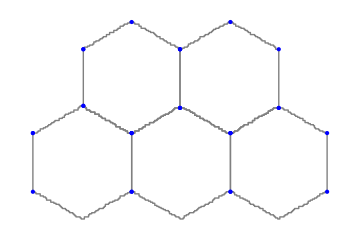

```mathematica
(* Test functions for gathering all the boundary, triple- and quad-junction pixels for a single randomly-chosen cell ID. *)
(* Then get all the neighboring cellIDs of that chosen cell; order the boundary pixels of all those cellIDs and display to check. *)

(* custom DistanceFunction used in FindShortestTour to make sure ordered boundary does not take diagonal steps *)
customDistanceFunction=(If[#1[[2,1]]-#2[[2,1]]==0||#1[[2,2]]-#2[[2,2]]==0,EuclideanDistance[#1[[2]],#2[[2]]]+If[Length[Intersection[#1[[1]],#2[[1]]]]==2,0,5],10000]&)

ci=RandomChoice[includedCellIDs];
ciList=Select[DeleteDuplicates[Flatten[Select[cellBoundaryPixels,MemberQ[#[[1]],ci]&][[All,1]]]],MemberQ[includedCellIDs,#]&];
orderedBoundaryPixels={};
Do[
cellBoundaryPixelsOneCell = Select[cellBoundaryPixels,MemberQ[#[[1]],ci]&];
(* custom DistanceFunction used in FindShortestTour to make sure ordered boundary does not take diagonal steps *)
boundaryPixelsOrder=FindShortestTour[cellBoundaryPixelsOneCell,DistanceFunction->customDistanceFunction][[2]];
orderedBoundaryPixelsOneCell=cellBoundaryPixelsOneCell[[boundaryPixelsOrder]];
AppendTo[orderedBoundaryPixels, orderedBoundaryPixelsOneCell]
,{ci,ciList}]
Print["Graphical check of ordered boundary pixel lists for a randomly-chosen cell and its neighbors: boundary points in gray, triple-junctions in blue, and quad-junctions in red."]
Graphics[{
PointSize[Medium],Gray,
Table[Line[orderedBoundaryPixelsOneCell[[All,2]]],{orderedBoundaryPixelsOneCell,orderedBoundaryPixels}],
Table[Switch[Length[#[[1]]],2,Null,3,{Blue,Point[#[[2]]]},4,{Red,Point[#[[2]]]}]&/@orderedBoundaryPixelsOneCell,{orderedBoundaryPixelsOneCell,orderedBoundaryPixels}]
},ImageSize->Medium]
```

```mathematica
(* Get an ordered list of boundary pixels for every included cellID. This step is fairly slow, but the evaluation monitor provides a readout of the calculation's progress. *)
orderedBoundaryPixels={};
nCells=Length[includedCellIDs];
ResourceFunction["SignedArea"][{{0,0},{1,0},{1,1},{0,1}}]; (* run this once just to make sure function is loaded into memory *)
timeReq=(Monitor[
Do[
cellBoundaryPixelsOneCell = Select[cellBoundaryPixels,MemberQ[#[[1]],includedCellIDs[[i]]]&];
(* custom DistanceFunction used in FindShortestTour to make sure ordered boundary does not take diagonal steps *)
boundaryPixelsOrder=FindShortestTour[cellBoundaryPixelsOneCell,DistanceFunction->customDistanceFunction][[2]];
orderedBoundaryPixelsOneCell=cellBoundaryPixelsOneCell[[boundaryPixelsOrder]];
cellArea=ResourceFunction["SignedArea"][orderedBoundaryPixelsOneCell[[All,2]]];
AppendTo[orderedBoundaryPixels, If[cellArea>=0,orderedBoundaryPixelsOneCell,Reverse[orderedBoundaryPixelsOneCell]]]
,{i,nCells}]
,"Ordering boundary of cell "<>ToString[i]<>" of "<>ToString[nCells]]//AbsoluteTiming)[[1]];
Print["Ordering all boundary locations took ",timeReq," s."]
```

Ordering all boundary locations took 52.8089 s.

All boundaryPixel lists are in correct CCW order.

Graphical check: ordered boundary points in gray, triple-junctions in blue, and quad-junctions in red.

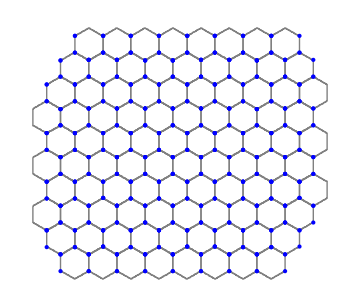

```mathematica
(* QA Checks *)
(* Confirm that all cell boundaries are in ccw order and thus yield a positive signed area. *)
areaList=ResourceFunction["SignedArea"][#[[All,2]]]&/@orderedBoundaryPixels;
nNegativeAreas=Length[Select[areaList,#<0&]];
If[nNegativeAreas==0, Print["All boundaryPixel lists are in correct CCW order."],Print["WARNING!! ",nNegativeAreas," cells have boundary pixels in incorrect CW order"]]

(* Make a graphic of all the orderedBoundaryPixels to check accuracy. *)
Print["Graphical check: ordered boundary points in gray, triple-junctions in blue, and quad-junctions in red."]
Graphics[{
PointSize[Small],Gray,
Table[Line[orderedBoundaryPixelsOneCell[[All,2]]],{orderedBoundaryPixelsOneCell,orderedBoundaryPixels}],
Table[Switch[Length[#[[1]]],2,Null,3,{Blue,Point[#[[2]]]},4,{Red,Point[#[[2]]]}]&/@orderedBoundaryPixelsOneCell,{orderedBoundaryPixelsOneCell,orderedBoundaryPixels}]
},ImageSize->Medium]
```

```mathematica
(* Gather edges by cell for all cells. *)
timeReq=(Monitor[
orderedBoundaryPixelsByCellByEdge={};
Do[
(* Print[i]; *)  
orderedBoundaryPixelsOneCell=  orderedBoundaryPixels[[i]];
(* ;;-2 is used to exclude the last pixel because it just repeats the first one *) 
tripleJunctionPairIndices=Partition[Flatten[Position[Length[#[[1]]]>=3&/@orderedBoundaryPixelsOneCell[[;;-2]],True]],2,1,1];
orderedBoundaryPixelsByEdge={};
Do[
{tji1,tji2}=tjpi;
(* ;;-2 is used to exclude the last pixel because it just repeats the first one *) 
selectedPixels=If[tji2>tji1,orderedBoundaryPixelsOneCell[[tji1;;tji2]],Join[orderedBoundaryPixelsOneCell[[tji1;;-2]],orderedBoundaryPixelsOneCell[[;;tji2]]]];
{tji1new,tji2new}=Flatten[Position[Length[#[[1]]]>=3&/@selectedPixels,True]];
orderedBoundaryPixelsOneEdge=selectedPixels;
(* confirm that all of the selected pixels have a common pair of adjacent cellIDs *) 
cellPairID=Intersection[orderedBoundaryPixelsOneEdge[[1,1]],orderedBoundaryPixelsOneEdge[[2,1]]];
commonCellIDPairQ=!MemberQ[ContainsAll[#,cellPairID]&/@orderedBoundaryPixelsOneEdge[[All,1]],False];
If[commonCellIDPairQ,AppendTo[orderedBoundaryPixelsByEdge,orderedBoundaryPixelsOneEdge],Print["WARNING!!! Not all pixels for edge group of cell " ,i," share a common bordering pair of cellIDs!"]];
,{tjpi,tripleJunctionPairIndices}];
AppendTo[orderedBoundaryPixelsByCellByEdge,orderedBoundaryPixelsByEdge]
,{i,nCells}];
,"Extracting boundary pixels by edge for cell "<>ToString[i]<>" of "<>ToString[nCells]]//AbsoluteTiming)[[1]];
Print["Gathering edges by cell for all cells took ",timeReq," s."]
```

Gathering edges by cell for all cells took 0.650114 s.

```mathematica
(* QA check that all cell-cell interfaces have been defined the same when considering the same pair of cells; only ordering should be reversed *)
orderedBoundaryPixelsByEdge=Flatten[orderedBoundaryPixelsByCellByEdge,1]; (* one-level of flattening removes the grouping of edges by cell *)
(* uncomment line below to add a mistake just to test the QA check function *)
(* orderedBoundaryPixelsByEdge[[-1,-2,2]]+={0.5,0.5} *)
cellPairIDsByEdge=Intersection[#[[1,1]],#[[2,1]]]&/@orderedBoundaryPixelsByEdge;
allBoundaryPixelsMatchQ=True;
nonmatchingBorderList={};
timeReq=(Monitor[
Do[
cpiText=cpi;
indexByEdge=Position[cellPairIDsByEdge,cpi];
correspondingBoundaryPixelsPair=orderedBoundaryPixelsByEdge[[First/@indexByEdge]];
boundaryPixelsMatchQ=MatchQ[correspondingBoundaryPixelsPair[[1]],Reverse[correspondingBoundaryPixelsPair[[2]]]];
allBoundaryPixelsMatchQ=allBoundaryPixelsMatchQ&&boundaryPixelsMatchQ;
If[!boundaryPixelsMatchQ,(
Print["WARNING!!! Boundary pixels for cell pair ",cpi," do match in the corresponding two cells."];
AppendTo[nonmatchingBorderList,correspondingBoundaryPixelsPair])]
,{cpi,Select[cellPairIDsByEdge,ContainsNone[excludedCellIDs,#]&]}]
,"Checking boundary pixels by edge for cell pair "<>ToString[cpiText]]//AbsoluteTiming)[[1]];
If[allBoundaryPixelsMatchQ,Print["Boundary pixels by edge match for all neighboring cell pairs"]]
If[!allBoundaryPixelsMatchQ,Print["Visualization of non-matching boundaries:"]]
If[!allBoundaryPixelsMatchQ,Graphics[{{RandomColor[],Line[#[[1,All,2]]]}&/@nonmatchingBorderList,{RandomColor[],Line[#[[2,All,2]]]}&/@nonmatchingBorderList}]]
If[!allBoundaryPixelsMatchQ,TableForm[{#[[1,All,2]],Reverse[#[[2,All,2]]]}]&/@nonmatchingBorderList]
Print["QA check for matching boundaries took ",timeReq," s."]
```

Boundary pixels by edge match for all neighboring cell pairs

QA check for matching boundaries took 0.199062 s.

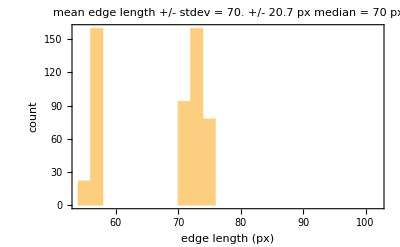

```mathematica
(* Get some stats on the edge lengths in the segmentation. These are needed for final smoothing and down-sampling steps in creating the mesh. *)
(* orderedBoundaryPixelsByEdge=Flatten[orderedBoundaryPixelsByCellByEdge,1]; *)(* one-level of flattening removes the grouping of edges by cell *)
edgeLengths=(Length[#]-1)&/@orderedBoundaryPixelsByEdge;
meanEdgeLength=N[Mean[edgeLengths]];
stdevEdgeLength=N[StandardDeviation[edgeLengths]];
medianEdgeLength=Median[edgeLengths];
plotLabel="mean edge length +/- stdev = "<>ToString[Round[meanEdgeLength,0.1]]<>" +/- "<>ToString[Round[stdevEdgeLength,0.1]]<>" px\n median = "<>ToString[medianEdgeLength]<>" px";
Histogram[edgeLengths,Frame->{{True,False},{True, False}},FrameLabel->{"edge length (px)","count"},PlotLabel->plotLabel]
```

```mathematica
(* Define a few simple moving-average smoothing functions. Could generalize, but options for 3, 5 and 7 point windows seem sufficient. *)
threePointSmoothing[orderedBoundaryPixelsOneEdge_]:=(
nPixels=Length[orderedBoundaryPixelsOneEdge];
If[nPixels>=3,
(cellIndices=orderedBoundaryPixelsOneEdge[[All,1]];
tj1=orderedBoundaryPixelsOneEdge[[1,2]];
tj2=orderedBoundaryPixelsOneEdge[[-1,2]];
Transpose[{cellIndices,Join[{tj1},MovingAverage[orderedBoundaryPixelsOneEdge[[All,2]],3],{tj2}]}])
,orderedBoundaryPixelsOneEdge]
)
fivePointSmoothing[orderedBoundaryPixelsOneEdge_]:=(
nPixels=Length[orderedBoundaryPixelsOneEdge];
If[nPixels>=5,
(cellIndices=orderedBoundaryPixelsOneEdge[[All,1]];
tj1=orderedBoundaryPixelsOneEdge[[1,2]];
tj2=orderedBoundaryPixelsOneEdge[[-1,2]];
smoothed3=MovingAverage[orderedBoundaryPixelsOneEdge[[All,2]],3];
smoothed5=MovingAverage[orderedBoundaryPixelsOneEdge[[All,2]],5];
Transpose[{cellIndices,Join[{tj1},{smoothed3[[1]]},smoothed5,{smoothed3[[-1]]},{tj2}]}])
,threePointSmoothing[orderedBoundaryPixelsOneEdge]]
)
sevenPointSmoothing[orderedBoundaryPixelsOneEdge_]:=(
nPixels=Length[orderedBoundaryPixelsOneEdge];
If[nPixels>=7,
(cellIndices=orderedBoundaryPixelsOneEdge[[All,1]];
tj1=orderedBoundaryPixelsOneEdge[[1,2]];
tj2=orderedBoundaryPixelsOneEdge[[-1,2]];
smoothed3=MovingAverage[orderedBoundaryPixelsOneEdge[[All,2]],3];
smoothed5=MovingAverage[orderedBoundaryPixelsOneEdge[[All,2]],5];
smoothed7=MovingAverage[orderedBoundaryPixelsOneEdge[[All,2]],7];
Transpose[{cellIndices,Join[{tj1},{smoothed3[[1]]},{smoothed5[[1]]},smoothed7,{smoothed5[[-1]]},{smoothed3[[-1]]},{tj2}]}])
,fivePointSmoothing[orderedBoundaryPixelsOneEdge]]
)
boundarySmoothing[orderedBoundaryPixelsOneEdge_,windowWidth_]:=(
Switch[windowWidth,
3,threePointSmoothing[orderedBoundaryPixelsOneEdge],
5,fivePointSmoothing[orderedBoundaryPixelsOneEdge],
7,sevenPointSmoothing[orderedBoundaryPixelsOneEdge],
_,orderedBoundaryPixelsOneEdge
]
)
```

Boundary smoothing applied to interfaces between triple- and quad-junctions of one cell. 
Triple- and quad-junctions are fixed. 
Red, green and blue correspond to 3-, 5- and 7-pt smoothing.

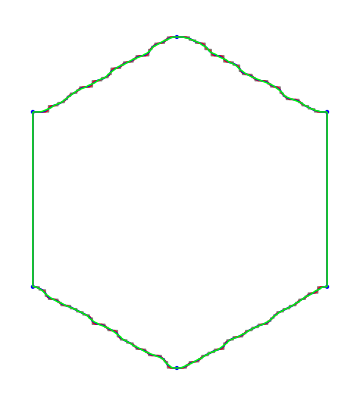

```mathematica
(* Test boundary smoothing functions on a single cell *)
(* First, build a list of interfaces or edges where each element is an orderedBoundaryPixel list specific to the interface between two cells with triple or quad junctions at the ends. *)
orderedBoundaryPixelsOneCell= RandomChoice[orderedBoundaryPixels];
(* In the step below, ;;-2 is used to exclude the last pixel because it just repeats the first one. *) 
tripleJunctionPairIndices=Partition[Flatten[Position[Length[#[[1]]]>=3&/@orderedBoundaryPixelsOneCell[[;;-2]],True]],2,1,1];

orderedBoundaryPixelsByEdge={};
Do[
(* Print["tjpi = ",tjpi]; *)
{tji1,tji2}=tjpi;
(* ;;-2 is used to exclude the last pixel because it just repeats the first one *) 
selectedPixels=If[tji2>tji1,orderedBoundaryPixelsOneCell[[tji1;;tji2]],Join[orderedBoundaryPixelsOneCell[[tji1;;-2]],orderedBoundaryPixelsOneCell[[;;tji2]]]];
(* Print[selectedPixels]; *)
{tji1new,tji2new}=Flatten[Position[Length[#[[1]]]>=3&/@selectedPixels,True]];
orderedBoundaryPixelsOneEdge=If[tji2new-tji1new==1,RotateLeft[selectedPixels,tji2new-1],selectedPixels];
(* confirm that all of the selected pixels have a common pair of adjacent cellIDs *) 
commonCellIDPairQ=!MemberQ[ContainsAll[#,Intersection[orderedBoundaryPixelsOneEdge[[1,1]],orderedBoundaryPixelsOneEdge[[2,1]]]]&/@orderedBoundaryPixelsOneEdge[[All,1]],False];
(* Print[orderedBoundaryPixelsOneEdge[[All,1]]]; *) 
If[commonCellIDPairQ,AppendTo[orderedBoundaryPixelsByEdge,orderedBoundaryPixelsOneEdge],Print["WARNING!!! Not all pixels for edge group share a common bordering pair of cellIDs!"]];
,{tjpi,tripleJunctionPairIndices}]
orderedBoundaryPixelsByEdgeSmoothed3=boundarySmoothing[#,3]&/@orderedBoundaryPixelsByEdge;
orderedBoundaryPixelsByEdgeSmoothed5=boundarySmoothing[#,5]&/@orderedBoundaryPixelsByEdge;
orderedBoundaryPixelsByEdgeSmoothed7=boundarySmoothing[#,7]&/@orderedBoundaryPixelsByEdge;
Print["Boundary smoothing applied to interfaces between triple- and quad-junctions of one cell. \nTriple- and quad-junctions are fixed. \nRed, green and blue correspond to 3-, 5- and 7-pt smoothing."]
Graphics[{Gray,Line[#[[All,2]]]&/@orderedBoundaryPixelsByEdge,PointSize[Medium],Blue,Point[#[[1,2]]]&/@orderedBoundaryPixelsByEdge,
Red,Line[#[[All,2]]]&/@orderedBoundaryPixelsByEdgeSmoothed3,
Blue,Line[#[[All,2]]]&/@orderedBoundaryPixelsByEdgeSmoothed5,
Green,Line[#[[All,2]]]&/@orderedBoundaryPixelsByEdgeSmoothed7}]
```

```mathematica
(* Define a function for smoothing and down-sampling a cell edge between two triple- or quad-junctions. *)
downsampleEdge[orderedBoundaryPixelsOneEdge_,targetΔs_,smoothingWindow_]:=(
cellPairIDs=Intersection[orderedBoundaryPixelsOneEdge[[1,1]],orderedBoundaryPixelsOneEdge[[2,1]]];
nSegments=Max[1,Round[Length[orderedBoundaryPixelsOneEdge]/targetΔs]];
nIntNodes=Max[0,nSegments-1];
orderedBoundaryPixelsOneEdgeSmoothed=boundarySmoothing[orderedBoundaryPixelsOneEdge,smoothingWindow];
edgeLengthSmoothed=ArcLength[Line[orderedBoundaryPixelsOneEdgeSmoothed[[All,2]]]];
parametricOrderedBoundaryPixelsOneEdgeSmoothed=Table[{If[i==1,0,ArcLength[Line[orderedBoundaryPixelsOneEdgeSmoothed[[;;i,2]]]]],orderedBoundaryPixelsOneEdgeSmoothed[[i,2,1]],orderedBoundaryPixelsOneEdgeSmoothed[[i,2,2]]},{i,Length[orderedBoundaryPixelsOneEdgeSmoothed[[All,2]]]}];
interpolatedEdgeX=Interpolation[parametricOrderedBoundaryPixelsOneEdgeSmoothed[[All,{1,2}]],InterpolationOrder->1];
interpolatedEdgeY=Interpolation[parametricOrderedBoundaryPixelsOneEdgeSmoothed[[All,{1,3}]],InterpolationOrder->1];
Δs=edgeLengthSmoothed/nSegments;
If[verbose&&localVerbose,Print["Down-sampled to have ",nIntNodes," intermediated nodes, each spaced by arc length of ",Δs]];
(* cellIndices=Join[{orderedBoundaryPixelsOneEdge[[All,1,1]]},Table[orderedBoundaryPixelsOneEdge[[All,1,2]],{k,nIntNodes}],orderedBoundaryPixelsOneEdge[[All,1,-1]]]; *) 
cellIndices=Append[orderedBoundaryPixelsOneEdge[[1;;(1+nIntNodes),1]],orderedBoundaryPixelsOneEdge[[-1,1]]];
(* Join[cellPairIDs,Table[{cellIndices[[i]],{interpolatedEdgeX[Δs*(i-1)],interpolatedEdgeY[Δs*(i-1)]}},{i,nSegments+1}]]; *)
Table[{cellIndices[[i]],{interpolatedEdgeX[Δs*(i-1)],interpolatedEdgeY[Δs*(i-1)]}},{i,nSegments+1}]
)
```

The target length for segments in the down-sampled mesh is 14. px.

Graphical comparison of down-sampling of a randomly-chosen edge and down-sampling of the same set of pixels in reverse order.

Down-sampled to have 3 intermediated nodes, each spaced by arc length of 14.

Down-sampled to have 3 intermediated nodes, each spaced by arc length of 14.

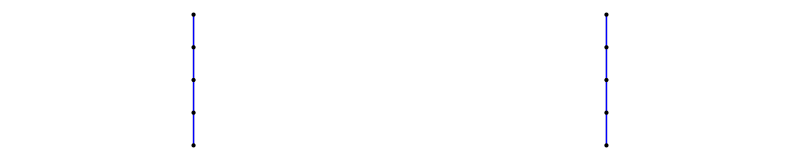

If working correctly, then these two down-sampled lists should be identical.

{{582.,824.},{582.,810.},{582.,796.},{582.,782.},{582.,768.}}

{{582.,824.},{582.,810.},{582.,796.},{582.,782.},{582.,768.}}

```mathematica
(* Check that the function works and returns identical points, just in reverse order, if the input points are reversed *)
targetΔs=N[medianEdgeLength/(targetNumberOfIntermediateNodes+1)];
Print["The target length for segments in the down-sampled mesh is ",targetΔs," px."]
localVerbose=True;
(* Test function against a randomly chosen edge *)
orderedBoundaryPixelsOneEdge=RandomChoice[orderedBoundaryPixelsByEdge];
Print["Graphical comparison of down-sampling of a randomly-chosen edge and down-sampling of the same set of pixels in reverse order."]
orderedBoundaryPixelsOneEdgeDownSampled=downsampleEdge[orderedBoundaryPixelsOneEdge,targetΔs,smoothingWindow];

orderedBoundaryPixelsOneEdgeReversedDownSampled=downsampleEdge[Reverse[orderedBoundaryPixelsOneEdge],targetΔs,smoothingWindow];
GraphicsRow[{Graphics[{Gray,Line[orderedBoundaryPixelsOneEdge[[All,2]]],PointSize[Medium],Blue,Line[orderedBoundaryPixelsOneEdgeSmoothed[[All,2]]],Black,PointSize[Medium],Point/@orderedBoundaryPixelsOneEdgeDownSampled[[All,2]]}],
Graphics[{Gray,Line[orderedBoundaryPixelsOneEdge[[All,2]]],PointSize[Medium],Blue,Line[orderedBoundaryPixelsOneEdgeSmoothed[[All,2]]],Black,PointSize[Medium],Point/@orderedBoundaryPixelsOneEdgeReversedDownSampled[[All,2]]}]
}]
Print["If working correctly, then these two down-sampled lists should be identical."]
orderedBoundaryPixelsOneEdgeDownSampled[[All,2]]
Reverse[orderedBoundaryPixelsOneEdgeReversedDownSampled[[All,2]]]
```

Down-sampling all edges took 52.2151 s.

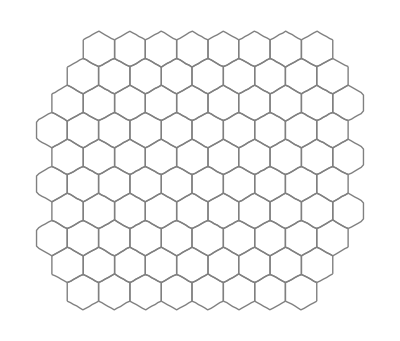

```mathematica
(* Use the function to down-sample all cell edges *)
localVerbose=False;
(* nEdges2=Length[orderedBoundaryPixelsByEdge[[All]]]; *)
(* Monitor[
orderedBoundaryPixelsByEdgeDownSampled=Table[downsampleEdge[orderedBoundaryPixelsByEdge[[j]],targetΔs,smoothingWindow],{j,nEdges2}];,
"Down-sampling cell edge "<>ToString[j]<>" of "<>ToString[nEdges2]] *)

timeReq=(Monitor[
orderedBoundaryPixelsByCellByEdgeDownSampled=Table[downsampleEdge[#,targetΔs,smoothingWindow]&/@orderedBoundaryPixelsByCellByEdge[[j]],{j,nCells}];,
"Down-sampling edges of cell "<>ToString[j]<>" of "<>ToString[nCells]]//AbsoluteTiming)[[1]];
Print["Down-sampling all edges took ",timeReq," s."]
(* Visual check of the down-sampled mesh. *)
Graphics[{Gray,Table[Line[#[[All,2]]]&/@orderedBoundaryPixelsByCellByEdgeDownSampled[[j]],{j,nCells}]}]
```

List of cell IDs adjacent to each node. Check that triple- and quad-junctions are not repeated (except the last one being the same as the first).

17039 | 23593 | 24248
23593 | 24248 | 
23593 | 24248 | 
23593 | 24248 | 
23593 | 24248 | 30146
24248 | 30146 | 
24248 | 30146 | 
24248 | 30146 | 
24248 | 30146 | 
24248 | 30146 | 30801
24248 | 30801 | 
24248 | 30801 | 
24248 | 30801 | 
24248 | 30801 | 
24248 | 24903 | 30801
24248 | 24903 | 
24248 | 24903 | 
24248 | 24903 | 
17694 | 24248 | 24903
17694 | 24248 | 
17694 | 24248 | 
17694 | 24248 | 
17694 | 24248 | 
17039 | 17694 | 24248
17039 | 24248 | 
17039 | 24248 | 
17039 | 24248 | 
17039 | 24248 | 
17039 | 23593 | 24248

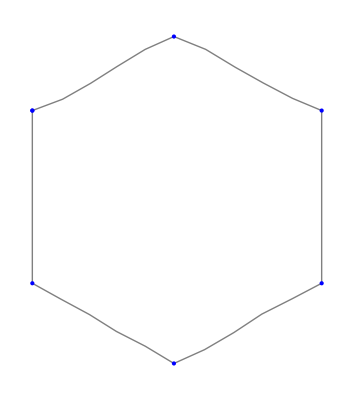

```mathematica
(* Need to reassemble orderedBoundaryPixelsByCellByEdgeDownSampled into orderedBoundaryPixelsByCellDownSampled so that the list of pixels goes around each entire cell *)
(* First test on a randomly selected cell *)
orderedBoundaryPixelsOneCellByEdgeDownSampled=RandomChoice[orderedBoundaryPixelsByCellByEdgeDownSampled];
(* put all the edge pixels back together into a single list; drop the 2nd triple junction of each edge except the last one, which should repeat the first triple juction of first edge *)
orderedBoundaryPixelsByCellDownSampled=Append[Flatten[orderedBoundaryPixelsOneCellByEdgeDownSampled[[All,;;-2]],1],orderedBoundaryPixelsOneCellByEdgeDownSampled[[-1,-1]]];
Print["List of cell IDs adjacent to each node. Check that triple- and quad-junctions are not repeated (except the last one being the same as the first)."]
Print[TableForm[orderedBoundaryPixelsByCellDownSampled[[All,1]]]]
Graphics[{Gray,Line[orderedBoundaryPixelsByCellDownSampled[[All,2]]],Blue,Point[#[[2]]]&/@Select[orderedBoundaryPixelsByCellDownSampled,Length[#[[1]]]>=3&]}]
```

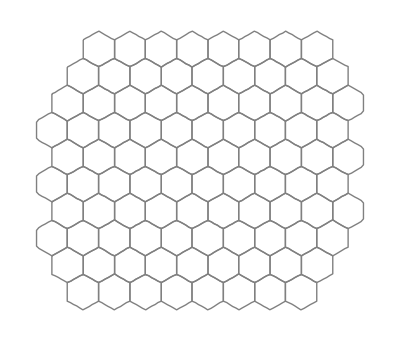

```mathematica
(* Now reassemble orderedBoundaryPixelsByCellByEdgeDownSampled into orderedBoundaryPixelsByCellDownSampled for cells *)orderedBoundaryPixelsByCellDownSampled=Append[Flatten[#[[All,;;-2]],1],#[[-1,-1]]]&/@orderedBoundaryPixelsByCellByEdgeDownSampled;
(* Visualize the reconstructed, down-sampled mesh *)
Graphics[{Gray,Table[Line[orderedBoundaryPixelsByCellDownSampled[[j,All,2]]],{j,nCells}]}]
```

```mathematica
(* Make a new neighborPairIndexList so entries correspond to index within cellRegionList rather than initial cellID. This version is more useful for later building matrices. *)
includedCellIDPositionList=PositionIndex[includedCellIDs];
neighborPairIndexList=Flatten[(#/.includedCellIDPositionList)]&/@neighborPairList;
Print["Substitions for replacing original cellIDs with position in cellRegionList (first 10 entries)"]
includedCellIDPositionList[[;;10]]
Print["First 10 entries in neighborPairList"]
neighborPairList[[;;10]]
Print["Corresponding 10 entries in neighborPairIndexList"]
neighborPairIndexList[[;;10]]
```

Substitions for replacing original cellIDs with position in cellRegionList (first 10 entries)

<|655→{1},1311→{2},1966→{3},2621→{4},3277→{5},3932→{6},4587→{7},5243→{8},7864→{9},8520→{10}|>

First 10 entries in neighborPairList

{{655,1311},{1311,1966},{1966,2621},{2621,3277},{3277,3932},{3932,4587},{4587,5243},{655,7864},{655,8520},{1311,8520}}

Corresponding 10 entries in neighborPairIndexList

{{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{1,9},{1,10},{2,10}}

```mathematica
Print["Visual check of final mesh (red) compared to input segmented image."]
Show[inputImage,Graphics[{Red,Table[Line[orderedBoundaryPixelsByCellDownSampled[[j,All,2]]],{j,nCells}]}],ImageSize->w/2]
```

Visual check of final mesh (red) compared to input segmented image.

-Graphics-

## 3-4 - Angle (Unit Vector) and Curvature Determination

This section will use the mesh generated above to estimate unit vectors (and thus angles) tangent to the directions at which each edge enters each triple- or quad-junction. It uses three methods for this estimation:
1. chord - unit vectors are determined by the direction from one triple- or quad-junction to the next (intermediate nodes are ignored);
2. nearest segment - unit vectors are determined by the direction from the triple- or quad-junction to the first intermediate node along the edge; and
3. arc fit approximation - each edge is fit to a parabolic approximation of a circular arc and the unit vectors are determined by the tangents to this arc fit at each triple- or quad-junction.
This section also uses the arc fit approximation to determine the curvature of each cell-cell interface.
Unit vectors are calculated using all three methods in this section. The user will be able to choose which one they prefer in the next section when the equations are setup to solve for the tensions and pressures.

```mathematica
verbose = False;  (* If verbose = True then lots of extra information is output. *)
```

```mathematica
(* Restructure lists to make it easier to calculate tangent vectors and curvatures. *)
nEdgesByCell=Length/@orderedBoundaryPixelsByCellByEdgeDownSampled;
edgeListForCellFITwithDuplicates={};
timeReq=(Monitor[
Do[
cellID1=includedCellIDs[[i]];
(* Print[cellID1]; *)
Do[
{tj1cellIDs,tj2cellIDs}=orderedBoundaryPixelsByCellByEdgeDownSampled[[i,j,{1,-1},1]];
cellIDPair=Intersection[tj1cellIDs,tj2cellIDs];
(* cellIDPair can end up with more than two cellIDs if both triple junctions connect same triplet of cells; can happen for a dangling cell on edge of patch *)
(* make an attempt to fix this by comparing cellIDs of intermediate nodes, but if unfixable, then exclude this edge *) 
If[Length[cellIDPair]>2,cellIDPair=Intersection[cellIDPair,orderedBoundaryPixelsByCellByEdgeDownSampled[[i,j,2,1]]]];  
orderedCellIDPair=If[cellIDPair[[1]]==cellID1,cellIDPair,Reverse[cellIDPair]];
AppendTo[edgeListForCellFITwithDuplicates,{orderedCellIDPair,{tj1cellIDs,tj2cellIDs},orderedBoundaryPixelsByCellByEdgeDownSampled[[i,j,All,2]]}];
,{j,nEdgesByCell[[i]]}]
,{i,nCells}]
,"Restructuring boundaryPixel list to CellFIT format for cell "<>ToString[i]<>" of "<>ToString[nCells]]//AbsoluteTiming)[[1]]
Print["Restructuring edgeList took ",timeReq," s."]
```

0.053518

Restructuring edgeList took 0.053518 s.

536

289

Deleting duplicates from edgeListForCellFIT took 0.107694 s.

Compare edgeListForCellFIT before and after deleting duplicates. Should look identical.

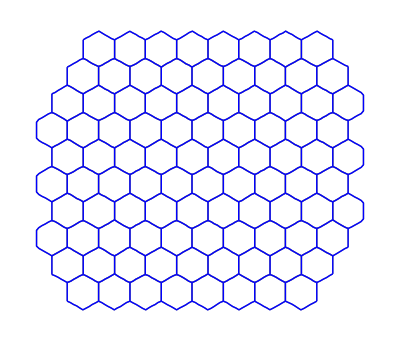

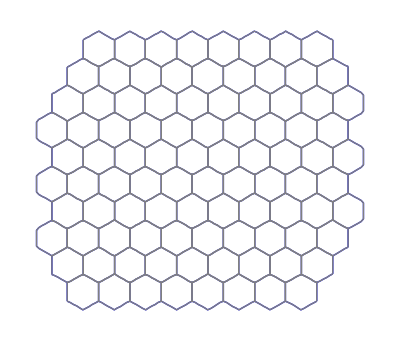

```mathematica
(* Delete duplicate edges; internal edges between cell pairs should show up in the list twice - just in reverse order *)
nBefore=Length[edgeListForCellFITwithDuplicates]
timeReq=AbsoluteTiming[
edgeListForCellFIT=DeleteDuplicates[edgeListForCellFITwithDuplicates,(#1[[2]]==Reverse[#2[[2]]])&];][[1]];
nAfter=Length[edgeListForCellFIT]
Print["Deleting duplicates from edgeListForCellFIT took ",timeReq," s."]
(* visual check that edge lists are still good after restructuring and deleting duplicates *)
Print["Compare edgeListForCellFIT before and after deleting duplicates. Should look identical."]
Graphics[{Gray,Line[#[[3]]]&/@edgeListForCellFITwithDuplicates,Blue,Line[#[[3]]]&/@edgeListForCellFIT}]
Graphics[{Blue,Line[#[[3]]]&/@edgeListForCellFIT,Gray,Line[#[[3]]]&/@edgeListForCellFITwithDuplicates}]
```

GRAY = cell edge; RED = chord-based vectors; BLUE = nearest-segment vectors; GREEN = arc-fit and its tangent vectors

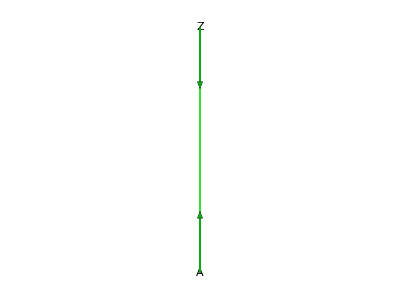

```mathematica
(* Select a cell edge (with at least 3 nodes) at random and compare methods for estimating tangent unit vectors *)
selectedEdge=RandomChoice[Select[edgeListForCellFIT,Length[#[[3]]]>3&]];

(* calculate TJ vectors via chords *)
{ptA,ptB,ptY,ptZ}=selectedEdge[[3,{1,2,-2,-1}]];
d=EuclideanDistance[ptA,ptZ];
vecAch=(ptZ-ptA)/d;
vecZch=-vecAch;
(* calculate TJ vectors via closest segment *)
vecAns=(ptB-ptA)/EuclideanDistance[ptA,ptB];
vecZns=(ptY-ptZ)/EuclideanDistance[ptY,ptZ];

(* calculate TJ vectors via tangent of arc fit *)
(* first rotate edge so that its chord is horizontal, with points running from right to left (ccw sense for cell at bottom), and shift coord so that midpoint is at origin *)
ptMid=(ptA+ptZ)/2;
θ=ArcTan[vecAch[[1]],vecZch[[2]]]/Degree; 
rotMatrix={{vecZch[[1]],vecZch[[2]]},{-vecZch[[2]],vecZch[[1]]}};
rotBackMatrix={{vecZch[[1]],-vecZch[[2]]},{vecZch[[2]],vecZch[[1]]}};
rotatedEdge=rotMatrix.(#-ptMid)&/@selectedEdge[[3]];

(* then fit the rotated line to a parabolic approximation of an arc of radius R (curvature κ = 1/R that is forced to go through the two endpoints *)
ΔyMax=Max[rotatedEdge[[2;;-2,2]]];
ptARot=rotatedEdge[[1]];
ptZRot=rotatedEdge[[-1]];
a=.
nlm=NonlinearModelFit[rotatedEdge[[2;;-2]],a x^2-a (d/2)^2,{{a,0}},x];
xMin=rotatedEdge[[1,1]];
xMax=rotatedEdge[[-1,1]];
If[verbose,Show[
ListPlot[rotatedEdge],
Plot[nlm[x],{x,xMin,xMax}]
]]
(* and use this fit to calculate the tangent vectors at the edge's endpoints *)
vecAarcRot={-1/Sqrt[1+(a*d)^2],-(a*d)/Sqrt[1+(a*d)^2]}/.nlm["BestFitParameters"];
vecZarcRot={1/Sqrt[1+(a*d)^2],-(a*d)/Sqrt[1+(a*d)^2]}/.nlm["BestFitParameters"];
(* rotate everything back to the original orientation of the edge *)
vecAarc=rotBackMatrix.vecAarcRot;
vecZarc=rotBackMatrix.vecZarcRot;

Print["GRAY = cell edge; RED = chord-based vectors; BLUE = nearest-segment vectors; GREEN = arc-fit and its tangent vectors"]
s=d/4; (* scaling factor for displaying the arrows representing the unit vectors *)
Graphics[{
Gray,Line[selectedEdge[[3]]],Black,Text["A",ptA],Text["Z",ptZ],
Red,Arrow[{ptA,ptA+s*vecAch}],Arrow[{ptZ,ptZ+s*vecZch}],
Blue,Arrow[{ptA,ptA+s*vecAns}],Arrow[{ptZ,ptZ+s*vecZns}],
Green,Line[(rotBackMatrix.#+ptMid)&/@Table[{x,nlm[x]},{x,-d/2,d/2,d/20}]],
Darker[Green],Arrow[{ptA,ptA+s*vecAarc}],Arrow[{ptZ,ptZ+s*vecZarc}]
}]
```

Estimating all triple- and quad-junction unit vectors took 0.581681 s.

Visual check of one randomly-selected edge and its unit vectors.

GRAY = cell edge; RED = chord-based vectors; BLUE = nearest-segment vectors; GREEN = arc-fit vectors

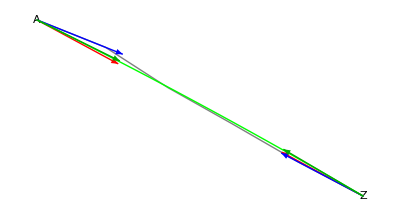

```mathematica
(* Apply the same methods to estimate the TJ unit vectors for all edges. Also estimates curvature of each edge. *)
(* All of this information is then stored in edgeListForCellFITplus *)
selectedEdgesForCellFIT=edgeListForCellFIT;
nEdgesToProcess=Length[selectedEdgesForCellFIT];
edgeListForCellFITplus={};
timeReq=(Monitor[
Do[
selectedEdge=selectedEdgesForCellFIT[[i]];
(* calculate TJ vectors via chords *)
{ptA,ptB,ptY,ptZ}=selectedEdge[[3,{1,2,-2,-1}]];
d=EuclideanDistance[ptA,ptZ];
vecAch=(ptZ-ptA)/d;
vecZch=-vecAch;
(* calculate TJ vectors via closest segment *)
vecAns=(ptB-ptA)/EuclideanDistance[ptA,ptB];
vecZns=(ptY-ptZ)/EuclideanDistance[ptY,ptZ];

(* calculate vectors via tangent of arc fit *)
(* first rotate edge so that its chord is horizontal, with points running from right to left (ccw sense for cell at bottom), and shift coord so that midpoint is at origin *)
ptMid=(ptA+ptZ)/2;
θ=ArcTan[vecAch[[1]],vecZch[[2]]]/Degree; 
rotMatrix={{vecZch[[1]],vecZch[[2]]},{-vecZch[[2]],vecZch[[1]]}};
rotBackMatrix={{vecZch[[1]],-vecZch[[2]]},{vecZch[[2]],vecZch[[1]]}};

rotatedEdge=rotMatrix.(#-ptMid)&/@selectedEdge[[3]];

If[Length[selectedEdge]==2,(vecAarc=vecAch; vecZarc=vecZch; κ=0;),
((* then fit the rotated line to a parabolic approximation of an arc of radius R (curvature κ = 1/R that is forced to go through the two endpoints *)
ptARot=rotatedEdge[[1]];
ptZRot=rotatedEdge[[-1]];
a=.;
nlm=NonlinearModelFit[rotatedEdge[[All]],a x^2-a (d/2)^2,{{a,0}},x];
xMin=rotatedEdge[[1,1]];
xMax=rotatedEdge[[-1,1]];
If[verbose,Show[
ListPlot[rotatedEdge],
Plot[nlm[x],{x,xMin,xMax}]
]];
κ=-2a/.nlm["BestFitParameters"];
vecAarcRot={-1/Sqrt[1+(a*d)^2],-(a*d)/Sqrt[1+(a*d)^2]}/.nlm["BestFitParameters"];
vecZarcRot={1/Sqrt[1+(a*d)^2],-(a*d)/Sqrt[1+(a*d)^2]}/.nlm["BestFitParameters"];
(* rotate everything back to the original orientation of the edge *)
vecAarc=rotBackMatrix.vecAarcRot;
vecZarc=rotBackMatrix.vecZarcRot;
)];
AppendTo[edgeListForCellFITplus,Join[selectedEdge,{{vecAch,vecZch},{vecAns,vecZns},{vecAarc,vecZarc,κ}}]];
If[False,Graphics[{
Gray,Line[selectedEdge[[3]]],Black,Text["A",ptA],Text["Z",ptZ],
Red,Arrow[{ptA,ptA+s*vecAch}],Arrow[{ptZ,ptZ+s*vecZch}],
Blue,Arrow[{ptA,ptA+s*vecAns}],Arrow[{ptZ,ptZ+s*vecZns}],
Green,Line[(rotBackMatrix.#+ptMid)&/@Table[{x,nlm[x]},{x,-d/2,d/2,d/20}]],
Darker[Green],Arrow[{ptA,ptA+s*vecAarc}],Arrow[{ptZ,ptZ+s*vecZarc}]
}]];
,{i,nEdgesToProcess}]
,"Estimating TJ vectors and curvature for edge "<>ToString[i]<>" of "<>ToString[nEdgesToProcess]]//AbsoluteTiming)[[1]];
Print["Estimating all triple- and quad-junction unit vectors took ",timeReq," s."]

selectedEdge=RandomChoice[Select[edgeListForCellFITplus,Length[#[[3]]]>3&]];
{ptA,ptZ}=selectedEdge[[3,{1,-1}]];
{vecAch,vecZch}=selectedEdge[[4]];
{vecAns,vecZns}=selectedEdge[[5]];
{vecAarc,vecZarc}=selectedEdge[[6,;;2]];
rotBackMatrix={{vecZch[[1]],-vecZch[[2]]},{vecZch[[2]],vecZch[[1]]}};
d=EuclideanDistance[ptA,ptZ];
ptMid=(ptA+ptZ)/2;
κ=selectedEdge[[6,-1]];
a=-κ/2;
Print["Visual check of one randomly-selected edge and its unit vectors. "]
Print["GRAY = cell edge; RED = chord-based vectors; BLUE = nearest-segment vectors; GREEN = arc-fit vectors"]
s=d/4; (* scaling factor for displaying the arrows representing the unit vectors *)
Graphics[{
Gray,Line[selectedEdge[[3]]],Black,Text["A",ptA],Text["Z",ptZ],
Red,Arrow[{ptA,ptA+s*vecAch}],Arrow[{ptZ,ptZ+s*vecZch}],
Blue,Arrow[{ptA,ptA+s*vecAns}],Arrow[{ptZ,ptZ+s*vecZns}],
Green,Line[(rotBackMatrix.#+ptMid)&/@Table[{x,a*x^2-a*(d/2)^2},{x,-d/2,d/2,d/20}]],
Darker[Green],Arrow[{ptA,ptA+s*vecAarc}],Arrow[{ptZ,ptZ+s*vecZarc}]
}]
```

Visual check of one randomly-selected edge and its unit vectors.

GRAY = cell edge; RED = chord-based vectors; BLUE = nearest-segment vectors; GREEN = arc-fit vectors

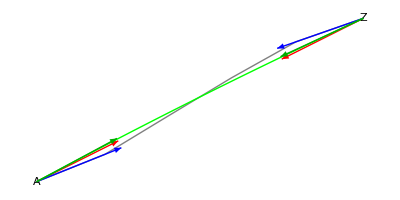

```mathematica
(* Can repeatedly evaluate this cell to test as many randomly-selected edges as you'd like *)
selectedEdge=RandomChoice[Select[edgeListForCellFITplus,Length[#[[3]]]>3&]];
{ptA,ptZ}=selectedEdge[[3,{1,-1}]];
{vecAch,vecZch}=selectedEdge[[4]];
{vecAns,vecZns}=selectedEdge[[5]];
{vecAarc,vecZarc}=selectedEdge[[6,;;2]];
rotBackMatrix={{vecZch[[1]],-vecZch[[2]]},{vecZch[[2]],vecZch[[1]]}};
d=EuclideanDistance[ptA,ptZ];
ptMid=(ptA+ptZ)/2;
κ=selectedEdge[[6,-1]];
a=-κ/2;
Print["Visual check of one randomly-selected edge and its unit vectors. "]
Print["GRAY = cell edge; RED = chord-based vectors; BLUE = nearest-segment vectors; GREEN = arc-fit vectors"]
s=d/4; (* scaling factor for displaying the arrows representing the unit vectors *)
Graphics[{
Gray,Line[selectedEdge[[3]]],Black,Text["A",ptA],Text["Z",ptZ],
Red,Arrow[{ptA,ptA+s*vecAch}],Arrow[{ptZ,ptZ+s*vecZch}],
Blue,Arrow[{ptA,ptA+s*vecAns}],Arrow[{ptZ,ptZ+s*vecZns}],
Green,Line[(rotBackMatrix.#+ptMid)&/@Table[{x,a*x^2-a*(d/2)^2},{x,-d/2,d/2,d/20}]],
Darker[Green],Arrow[{ptA,ptA+s*vecAarc}],Arrow[{ptZ,ptZ+s*vecZarc}]
}]
```

```mathematica
Print["Visual check of each method of estimating unit vectors compared to input segmented image."]
Print["RED = chord-based vectors; BLUE = nearest-segment vectors; GREEN = arc-fit vectors"]
unitVecs1={Line[{#[[3,1]],#[[3,1]]+s*#[[4,1]]}],Line[{#[[3,-1]],#[[3,-1]]+s*#[[4,2]]}]}&/@edgeListForCellFITplus;
unitVecs2={Line[{#[[3,1]],#[[3,1]]+s*#[[5,1]]}],Line[{#[[3,-1]],#[[3,-1]]+s*#[[5,2]]}]}&/@edgeListForCellFITplus;
unitVecs3={Line[{#[[3,1]],#[[3,1]]+s*#[[6,1]]}],Line[{#[[3,-1]],#[[3,-1]]+s*#[[6,2]]}]}&/@edgeListForCellFITplus;
Show[inputImage,Graphics[{Red,unitVecs1,Blue,unitVecs2, Green, unitVecs3} ],PlotRange->All,ImageSize->w/2]
Print["Close up of center of field of view."]
closeUpRange={{Max[0,w/2 - 8*medianEdgeLength],Min[w,w/2+ 8*medianEdgeLength]},{Max[0,h/2- 8*medianEdgeLength],Min[h,h/2+ 8*medianEdgeLength]}};
Show[inputImage,Graphics[{Red,unitVecs1,Blue,unitVecs2, Green, unitVecs3} ],PlotRange->closeUpRange,ImageSize->w/2]
```

Visual check of each method of estimating unit vectors compared to input segmented image.

RED = chord-based vectors; BLUE = nearest-segment vectors; GREEN = arc-fit vectors

-Graphics-

Close up of center of field of view.

-Graphics-

```mathematica
edgeListForCellFITplus[[1]]
```

{{655,0},{{0,655,6554},{0,655,7864}},{{162.,904.},{162.,890.},{162.,876.},{162.,862.},{162.,848.}},{{0.,-1.},{0.,1.}},{{0.,-1.},{0.,1.}},{{0.,-1.},{0.,1.},0.}}

```mathematica
Print["Visual check of arc-fit curvature estimates (red) overlaid on input segmented image."]
a=.; d=.; ptMid=.; rotBackMatrix=.;
subList={a->-#[[6,-1]]/2,d->EuclideanDistance[#[[3,1]],#[[3,-1]]],ptMid->(#[[3,1]]+#[[3,-1]])/2,rotBackMatrix->{#[[4,-1]]*{1,-1},Reverse[#[[4,-1]]]}}&/@edgeListForCellFITplus;
arcs=Table[Line[(rotBackMatrix.#+ptMid)&/@Table[{x,a x^2 - a (d/2)^2},{x,-d/2,d/2,d/20}]/.sub],{sub,subList}];
Show[inputImage,Graphics[{Red,arcs}],ImageSize->w/2]
Show[inputImage,Graphics[{Red,Thick,arcs}],PlotRange->closeUpRange,ImageSize->w/2]
```

Visual check of arc-fit curvature estimates (red) overlaid on input segmented image.

-Graphics-

-Graphics-

## 5-6 - Assemble, Constrain and Solve Tension (Young) Equations

This section sets up the matrices representing the systems of equations used to solve for the tensions and pressures. For the tensions, we have G_γγ = {0} where γ is the list of tensions, G_γ is a matrix of directional sines and cosines based on the tangent vectors for each edge at each triple- or quad-junction, and {0} is just a list of zeros implying quasi-equilibrium. Since this equation is homogeneous and we are not interested in the γ = {0} solution, we use a Lagrange multiplier to constrain the solution such that the average γ is equal to 1. The augmented (constrained) system of equations for the tensions is then:
-Graphics-
This system is typically overdetermined and solved using a linear least-squares approach.

The user can select among three methods for estimating the tangent vectors for each edge at each triple- or quad-junction:
1. chord - unit vectors are determined by the direction from one triple - or quad - junction to the next (intermediate nodes are ignored);
2. nearest segment - unit vectors are determined by the direction from the triple - or quad - junction to the first intermediate node along the edge; and
3. arc fit approximation - each edge is fit to a parabolic approximation of a circular arc and the unit vectors are determined by the tangents to this arc fit at each triple - or quad - junction .

```mathematica
tangentVectorMethod=2; (* 1=chord, 2=nearest segment, 3=arc fit approx. *)
verbose=False;     (* If verbose = True then lots of extra information is output. *)
```

247

Nodes at which force balance will be considered are in RED;
Edges across which pressure balance will be considered are in BLUE;
Excluded nodes and edges are GRAY.

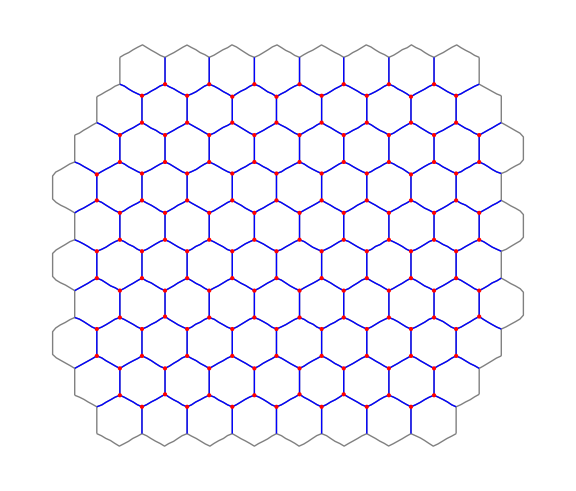

Will setup 308 equations for force balance at nodes to solve for 247 edge tensions.

Will setup 247 equations for pressure balance across edges to solve for 94 pressures.

```mathematica
(* To build Gγ and Gp matrices, we first need to get lists that will match up with the dimensions of those matrices to ease indexing. *)
edgeListForCellFITRagged=Select[edgeListForCellFITplus,ContainsNone[excludedCellIDs,#[[1]]]&];
nγ=Length[edgeListForCellFITRagged];
cellPairIDsRagged=edgeListForCellFITRagged[[All,1]];
nEqnsP=Length[cellPairIDsRagged]
tjIDs=DeleteDuplicates[Flatten[Transpose/@edgeListForCellFITRagged[[All,2;;3,{1,-1}]],1]];
tjIDsRagged=Select[tjIDs,ContainsNone[excludedCellIDs,#[[1]]]&];
nEqnsγ=2*Length[tjIDsRagged];
(* Visualize the 'ragged' lists to make sure the correct edges and TJs have been selected *)
Print["Nodes at which force balance will be considered are in RED;\nEdges across which pressure balance will be considered are in BLUE;\nExcluded nodes and edges are GRAY."]
Graphics[{Gray, Line[#[[3]]]&/@edgeListForCellFIT,Blue,, Line[#[[3]]]&/@edgeListForCellFITRagged,Red,Point[#[[2]]]&/@tjIDsRagged},ImageSize->Large]
Print["Will setup ",nEqnsγ," equations for force balance at nodes to solve for ",nγ," edge tensions."]
Print["Will setup ",nEqnsP," equations for pressure balance across edges to solve for ",nCells," pressures."]
```

```mathematica
(* Test steps to build the sparse array rules for a single randomly-selected edge *)
ruleListGγ={};
j=RandomInteger[nγ];
selectedEdge=edgeListForCellFITRagged[[j]]

Print["tangentVectorMethod = ",Switch[tangentVectorMethod,1,"chord",2,"nearest segment",3,"arc fit",_,"?unknown?"]]
Do[
tjID=selectedEdge[[2,k]];
If[ContainsNone[excludedCellIDs,tjID],
iNode=First@First@Position[tjIDsRagged[[All,1]],tjID];
Print["iNode = ",iNode];
ruleX={2*iNode,j}->selectedEdge[[tangentVectorMethod+3,k,1]];
ruleY={2*iNode+1,j}->selectedEdge[[tangentVectorMethod+3,k,2]] ;
Print["\tRule for putting values into an x-row of Gγ: ",ruleX];
Print["\tRule for putting values into an y-row of Gγ: ",ruleY]];
,{k,2}]
```

{{57015,64880},{{57015,60948,64880},{57015,57671,64880}},{{676.,176.},{685.257,180.128},{694.424,185.712},{703.182,191.364},{712.205,196.41},{722.,200.}},{{0.886585,0.462566},{-0.886585,-0.462566}},{{0.913289,0.407313},{-0.938922,-0.34413}},{{0.864655,0.502366},{-0.906684,-0.421811},-0.001753}}

tangentVectorMethod = nearest segment

iNode = 151

Rule for putting values into an x-row of Gγ: {302,235}→0.913289

Rule for putting values into an y-row of Gγ: {303,235}→0.407313

iNode = 152

Rule for putting values into an x-row of Gγ: {304,235}→-0.938922

Rule for putting values into an y-row of Gγ: {305,235}→-0.34413

```mathematica
(* Loop over edgeListForCellFITRagged to build all sparse array rules for Gγ matrix *)
ruleListGγ={};
timeReq=(Monitor[
Do[
Do[
selectedEdge=edgeListForCellFITRagged[[j]];
tjID=selectedEdge[[2,k]];
If[ContainsNone[excludedCellIDs,tjID],
iNode=First@First@Position[tjIDsRagged[[All,1]],tjID];
ruleX={2*iNode-1,j}->selectedEdge[[tangentVectorMethod+3,k,1]];
ruleY={2*iNode,j}->selectedEdge[[tangentVectorMethod+3,k,2]] ;
AppendTo[ruleListGγ,ruleX];
AppendTo[ruleListGγ,ruleY]];
,{k,2}];
,{j,nγ}]
,"Adding rules for TJs of edge # "<>ToString[j]<>" of "<>ToString[nγ]]//AbsoluteTiming)[[1]];
Print["Assembling all sparse array rules for constructing Gγ took ",timeReq," s."]
Print["Last 10 rules: ",ruleListGγ[[-10;;]]]
```

Assembling all sparse array rules for constructing Gγ took 0.119801 s.

Last 10 rules: {{293,243}→0.,{294,243}→-1.,{297,244}→0.,{298,244}→-1.,{301,245}→0.,{302,245}→-1.,{289,246}→0.,{290,246}→-1.,{305,247}→0.,{306,247}→-1.}

```mathematica
(* Use rules to construct Gγ *)
Gγ=SparseArray[ruleListGγ]
```

SparseArray[…]

```mathematica
(* Build the sparse augmented matrix GγAug using constraint that average γ is equal to 1 *)
constraintRules1=Table[{i,nγ+1}->1.,{i,nγ}];
constraintRules2=Table[{nγ+1,i}->1.,{i,nγ}];
Print["Check that rules in Gγ^T.Gγ and the constraint rows and columns are formatted correctly."]
ArrayRules[Transpose[Gγ].Gγ][[-10;;]]
constraintRules1[[-10;;]]
constraintRules2[[-10;;]]
Print["Assembling the complete constraint-augmented matrix GγAug"]
GγAug=SparseArray[Join[ArrayRules[Transpose[Gγ].Gγ][[;;-2]],constraintRules1,constraintRules2]]
```

Check that rules in Gγ^T.Gγ and the constraint rows and columns are formatted correctly.

{{245,234}→-0.371867,{245,235}→-0.407313,{245,245}→1.,{246,225}→-0.379959,{246,226}→-0.447214,{246,246}→1.,{247,237}→-0.454963,{247,238}→-0.394431,{247,247}→1.,{_,_}→0.}

{{238,248}→1.,{239,248}→1.,{240,248}→1.,{241,248}→1.,{242,248}→1.,{243,248}→1.,{244,248}→1.,{245,248}→1.,{246,248}→1.,{247,248}→1.}

{{248,238}→1.,{248,239}→1.,{248,240}→1.,{248,241}→1.,{248,242}→1.,{248,243}→1.,{248,244}→1.,{248,245}→1.,{248,246}→1.,{248,247}→1.}

Assembling the complete constraint-augmented matrix GγAug

SparseArray[…]

SparseArray[…]

Check first 10 values of γAug to make sure they are numeric and of reasonable size: {1.22353,1.19035,1.07107,1.29178,1.24611,0.904955,1.16287,1.14127,0.884005,1.11678}

Confirm that the average of all γ is equal to 1. <γ> = 1.

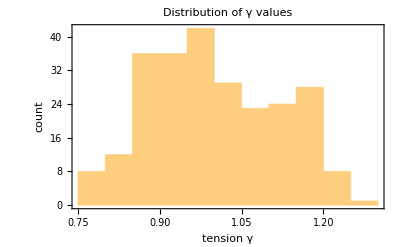

```mathematica
(* Construct the sparse array y with all zeros except the value nγ in the last row *)
y=SparseArray[{nγ+1,1}->nγ]
(* and solve the matrix equation for the best least-squares estimates of all tensions *)
γAug=Flatten[Inverse[GγAug].y];
Print["Check first 10 values of γAug to make sure they are numeric and of reasonable size: ",γAug[[;;10]]]
Print["Confirm that the average of all γ is equal to 1. <γ> = ",Mean[γAug[[;;-2]]]] 
(* Note that ;;-2 is used to exclude the last entry of γAug which is not a tension but is instead the Lagrange multiplier. *)
Histogram[γAug[[;;-2]], Frame->{{True, False},{True,False}},FrameLabel->{"tension γ","count"},PlotLabel->"Distribution of γ values"]
```

Tension map with ends of color scale at 10th and 90th percentile of tension distribution (0.861519 to 1.17146).

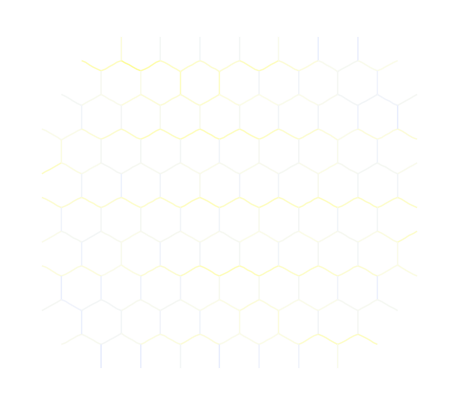

```mathematica
(* Map the standard tensions across the image using the 10th and 90th percentile values as the range of the color mapping  *)
(* More extensive visualization will be provided in Section 10 *)
colorScheme="TemperatureMap";
minPercentile=0.10;
maxPercentile=0.90;
γSorted=Sort[γAug[[;;-2]]];
γMin=γSorted[[Round[minPercentile*(nγ-1),1]+1]];
γMax=γSorted[[Round[maxPercentile*(nγ-1),1]+1]];
Print["Tension map with ends of color scale at 10th and 90th percentile of tension distribution (",γMin," to ",γMax,")." ]
iOfγMin=Position[γAug,γMin][[1]];
iOfγMax=Position[γAug,γMax][[1]];
forceZeroToMiddle=True;
γColorList=ColorData[{colorScheme,{γMin-1,γMax+1}}][#]&/@γAug[[;;-2]];
γMap=Graphics[{Table[{γColorList[[i]],Line[edgeListForCellFITRagged[[i,3]]]},{i,nγ}]}]
```

Check first 10 γ values with standard errors to make sure they are numeric and reasonable: {1.220.16,1.190.14,1.070.14,1.290.15,1.250.13,0.900.12,1.160.12,1.140.12,0.880.12,1.120.11}

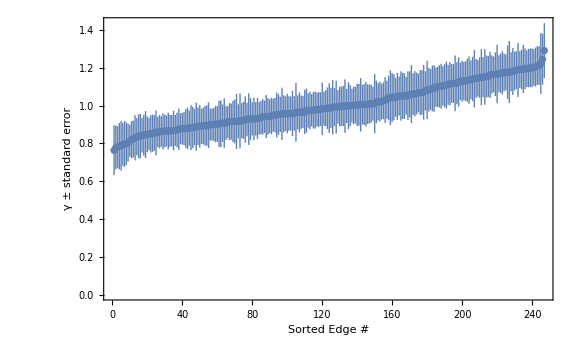

```mathematica
(* Since we are using least squares, the best fit estimates also have confidence limits from standard errors *)
(* Estimate the standard errors for γ from the covariance matix *)
γResiduals=Gγ.γAug[[;;-2]];
SSRγ=Transpose[γResiduals].γResiduals;
σγ=Sqrt[SSRγ/(nEqnsγ-nγ)];
COVγ=Inverse[GγAug];
γStError=σγ*Sqrt[#]&/@Diagonal[COVγ][[;;-2]];
γWithStError=Table[Around[γAug[[i]],γStError[[i]]],{i,nγ}];
Print["Check first 10 γ values with standard errors to make sure they are numeric and reasonable: ",γWithStError[[;;10]]]
ListPlot[Sort[γWithStError],Axes->{False,True},Frame->{{True,False},{True,False}},FrameLabel-> {"Sorted Edge #","γ ± standard error"},FrameStyle->Directive[14],PlotRange->Automatic,ImageSize->Large]
```

## 7-8 - Assemble, Constrain and Solve Pressure (Laplace) Equations

For the pressures, the system of equations is based on a Laplace pressure balance across each cell edge, i.e., Δp_ij=γ_ij/ρ_ij=γ_ij κ_ij where the pressure difference between cells i and j (Δp) is balanced by tension (γ) along the curved edge, characterized either by its radius of curvature (ρ) or its curvature itself (κ = 1/ρ). The curvature itself is typically easier to handle in calculations because it remains finite when edges become flat. Based on this Laplace pressure balance, we build the system of equations G_pp = q where p is the list of pressures, q is a list in which the curvature of each edge (κ) has been multiplied by the previously-solved-for tension along that edge (γ). Each row of matrix G_pcontains just two non-zero entries: a single +1 and a single -1 corresponding to the two cells bordering each edge. This system of equations also has non-unique solutions because an arbitrary constant could be added to any set of pressure solutions. We thus use another Lagrange multiplier to constrain the solution. In this case we constrain the average pressure to be zero. The augmented (constrained) system of equations for the pressures is then:

-Graphics-
 This system is also typically overdetermined and solved using a linear least-squares approach.

```mathematica
verbose=False;     (* If verbose = True then lots of extra information is output. *)
```

```mathematica
(* Loop over edgeListForCellFITRagged to build all sparse array rules for Gp matrix *)
ruleListGp={};
timeReq=(Monitor[
Do[
selectedEdge=edgeListForCellFITRagged[[i]];
{cellID1,cellID2}=selectedEdge[[1]];
j1=First@First@Position[includedCellIDs,cellID1];
j2=First@First@Position[includedCellIDs,cellID2];
AppendTo[ruleListGp,{i,j1}->1];
AppendTo[ruleListGp,{i,j2}->-1];
,{i,nγ}]
,"Adding rules for TJs of edge # "<>ToString[j]<>" of"<>ToString[nγ]]//AbsoluteTiming)[[1]];
Print["Assembling all sparse array rules for constructing Gp took ",timeReq," s."]
Print["Last 10 rules: ",ruleListGp[[-10;;]]]
(* Use curvatures from arc fits and previously-solved-for tensions to construct q array *)
q=Table[γAug[[i]]*edgeListForCellFITRagged[[i,-1,-1]],{i,nγ}];
Print["Last 10 values in q array: ",q[[-10;;]]]
```

Assembling all sparse array rules for constructing Gp took 0.055825 s.

Last 10 rules: {{243,88}→1,{243,92}→-1,{244,88}→1,{244,89}→-1,{245,89}→1,{245,93}→-1,{246,91}→1,{246,92}→-1,{247,93}→1,{247,94}→-1}

Last 10 values in q array: {-0.000415039,0.,-0.0017472,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(* Use rules to construct Gp *)
Gp=SparseArray[ruleListGp]
```

SparseArray[…]

```mathematica
(* Build the sparse augmented matrix GpAug using constraint that average p is equal to 0 *)
constraintRules1=Table[{i,nCells+1}->1.,{i,nCells}]; (* column of 1s *)
constraintRules2=Table[{nCells+1,i}->1.,{i,nCells}];   (* row of 1s *)
Print["Check that rules in Gp^T.Gp and the constraint rows and columns are formatted correctly."]
ArrayRules[Transpose[Gp].Gp][[-10;;]]
constraintRules1[[-10;;]]
constraintRules2[[-10;;]]
Print["Assembling the complete constraint-augmented matrix GpAug"]
GpAug=SparseArray[Join[ArrayRules[Transpose[Gp].Gp][[;;-2]],constraintRules1,constraintRules2]]
```

Check that rules in Gp^T.Gp and the constraint rows and columns are formatted correctly.

{{93,84}→-1,{93,93}→4,{93,85}→-1,{93,89}→-1,{93,94}→-1,{94,85}→-1,{94,94}→3,{94,86}→-1,{94,93}→-1,{_,_}→0}

{{85,95}→1.,{86,95}→1.,{87,95}→1.,{88,95}→1.,{89,95}→1.,{90,95}→1.,{91,95}→1.,{92,95}→1.,{93,95}→1.,{94,95}→1.}

{{95,85}→1.,{95,86}→1.,{95,87}→1.,{95,88}→1.,{95,89}→1.,{95,90}→1.,{95,91}→1.,{95,92}→1.,{95,93}→1.,{95,94}→1.}

Assembling the complete constraint-augmented matrix GpAug

SparseArray[…]

SparseArray[…]

Check first 10 values of pAug to make sure they are numeric and of reasonable size: {0.00116942,0.00191413,-0.000238274,-3.20695×10^-7,0.00200978,0.000994905,-0.0006504,0.000498599,-0.000357432,0.000814271}

Confirm that the average of all p is equal to 0. <p> = -2.07613×10^-20

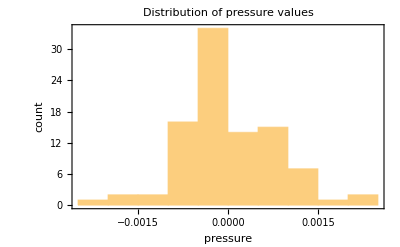

```mathematica
(* Construct the sparse array qAug = Gp.q with an extra 0 added onto end for <p> = 0 constraint *)
qAug=SparseArray[Join[ArrayRules[Transpose[Gp].q][[;;-2]],{{nCells+1}->0}]]
(* and solve the matrix equation for the best least-squares estimates of all pressures *)
pAug=Flatten[Inverse[GpAug].qAug];
Print["Check first 10 values of pAug to make sure they are numeric and of reasonable size: ",pAug[[;;10]]]
Print["Confirm that the average of all p is equal to 0. <p> = ",Mean[pAug[[;;-2]]]] 
(* Note that ;;-2 is used to exclude the last entry of pAug which is not a tension but is instead the Lagrange multiplier. *)
Histogram[pAug[[;;-2]], Frame->{{True, False},{True,False}},FrameLabel->{"pressure","count"},PlotLabel->"Distribution of pressure values"]
```

Pressure map with ends of color scale at 10th and 90th percentile of pressure distribution (-0.00083253 to 0.00100839).

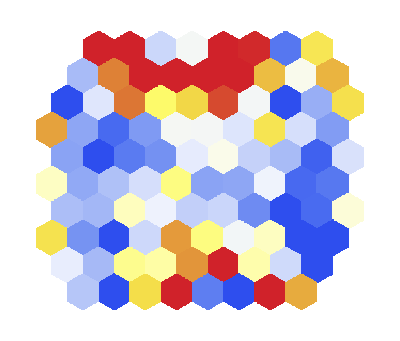

```mathematica
(* Map the standard pressures across the image using the 10th and 90th percentile values as the range of the color mapping  *)
(* More extensive visualization will be provided in Section 10 *)
colorScheme="TemperatureMap";
minPercentile=0.10;
maxPercentile=0.90;
pSorted=Sort[pAug[[;;-2]]];
pMin=pSorted[[Round[minPercentile*(nCells-1),1]+1]];
pMax=pSorted[[Round[maxPercentile*(nCells-1),1]+1]];
forceZeroToMiddle=True;
pColorList=ColorData[{colorScheme,{pMin,pMax}}][#]&/@pAug[[;;-2]];
Print["Pressure map with ends of color scale at 10th and 90th percentile of pressure distribution (",pMin," to ",pMax,")." ]
pMap=Graphics[{Table[{pColorList[[i]],cellRegionList[[i]]},{i,nCells}]}]
```

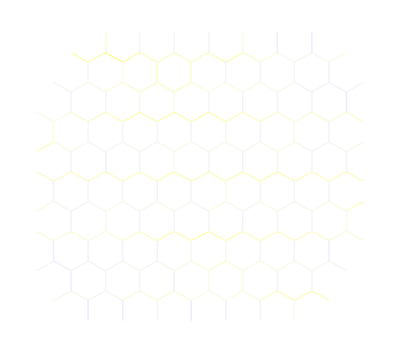

-Graphics-

```mathematica
(* View the tension and pressure maps side-by-side; more visualization in Section 10 *)
γMap
pMap
```

Check first 10 pressure values with standard errors to make sure they are numeric and reasonable: {0.00120.0009,0.00190.0008,-0.00020.0007,0.00000.0007,0.00200.0007,0.00100.0007,-0.00070.0008,0.00050.0009,-0.00040.0008,0.00080.0007}

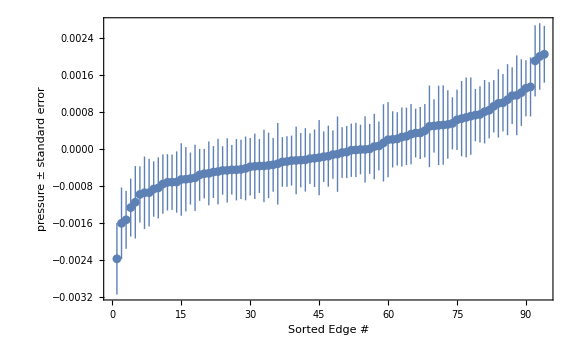

```mathematica
(* Since we are using least squares, the best fit estimates also have confidence limits from standard errors *)
(* Estimate the standard errors for pressures from the covariance matix *)
pResiduals=Gp.pAug[[;;-2]]-q;
SSRp=Transpose[pResiduals].pResiduals;
σp=Sqrt[SSRp/(nγ-nCells)];
COVp=Inverse[GpAug];
pStError=σp*Sqrt[#]&/@Diagonal[COVp][[;;-2]];
pWithStError=Table[Around[pAug[[i]],pStError[[i]]],{i,nCells}];
Print["Check first 10 pressure values with standard errors to make sure they are numeric and reasonable: ",pWithStError[[;;10]]]
ListPlot[Sort[pWithStError],Axes->{False,True},Frame->{{True,False},{True,False}},FrameLabel-> {"Sorted Edge #","pressure ± standard error"},FrameStyle->Directive[14],PlotRange->Automatic,ImageSize->Large]
```

## 9-10 Display and Evaluate Solutions

The γAug and pAug arrays have lists of the so-called standard tensions and pressures, i.e., those that result from applying the constraints < γ> = 1 and < p > = 0. Additional solutions can be found by multiplying all tensions and pressures by a a single scalar. You can also add any constant value to all the pressures (since only pressure differences matter). The cells in this section demonstrate some ways to visualize and to rescale the combined tension and pressure solutions.

Overlay of the tension and pressure maps

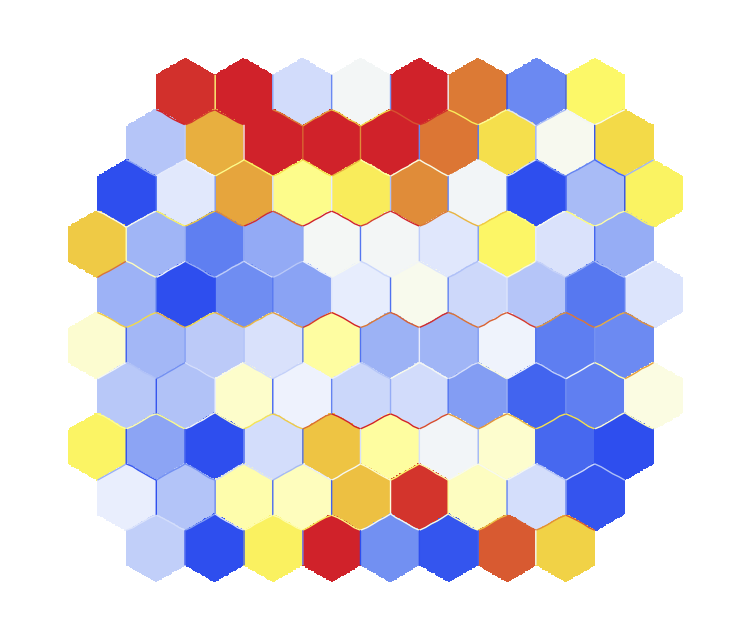

Side-by-side plots of the tension and pressure maps

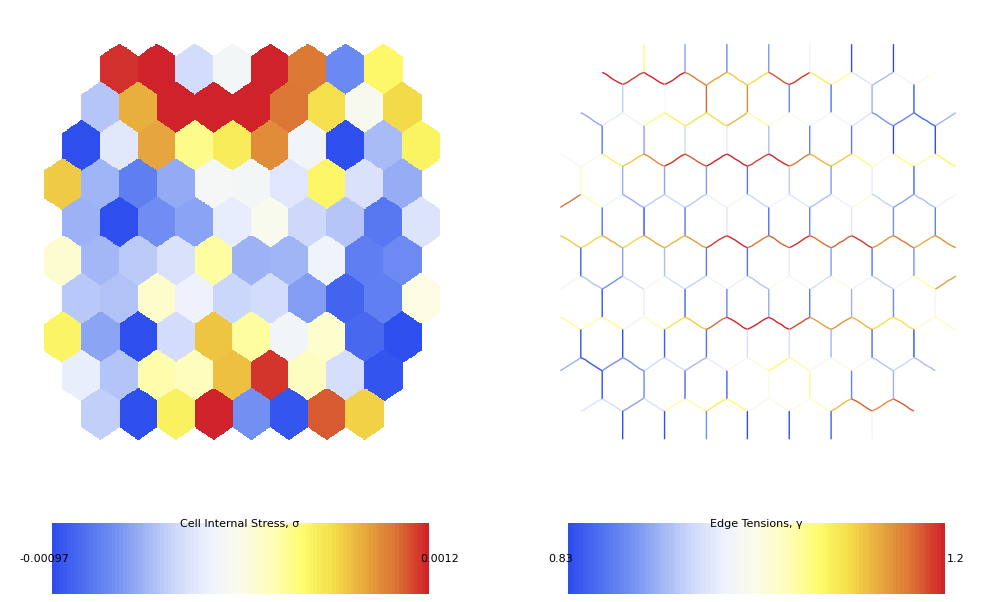

```mathematica
(* Visualize the tension and pressure solutions together *)
(* Change the three parameters below to alter the color scheme and limits for displaying the pressures *)
pColorScheme="TemperatureMap";
minPercentile=0.05;
maxPercentile=0.95;

pSorted=Sort[pAug[[;;-2]]];
(* ResourceFunction["DecimalRound"][expr, #SigFigs] *)
pMin=ResourceFunction["DecimalRound"][pSorted[[Round[minPercentile*(nCells-1),1]+1]],2];
pMax=ResourceFunction["DecimalRound"][pSorted[[Round[maxPercentile*(nCells-1),1]+1]],2];
pColorList=ColorData[{pColorScheme,{pMin,pMax}}][#]&/@pAug[[;;-2]];
pMap=Graphics[{Table[{pColorList[[i]],cellRegionList[[i]]},{i,nCells}]}];

(* Change the three parameters below to alter the color scheme and limits for displaying the tensions *)
γColorScheme="TemperatureMap";
minPercentile=0.05;
maxPercentile=0.95;

γSorted=Sort[γAug[[;;-2]]];
γMin=ResourceFunction["DecimalRound"][γSorted[[Round[minPercentile*(nγ-1),1]+1]],2];
γMax=ResourceFunction["DecimalRound"][γSorted[[Round[maxPercentile*(nγ-1),1]+1]],2];
γColorList=ColorData[{γColorScheme,{γMin,γMax}}][#]&/@γAug[[;;-2]];
γMap=Graphics[{Table[{γColorList[[i]],Line[edgeListForCellFITRagged[[i,3]]]},{i,nγ}]}];

(* Overlay of both solution maps *)
Print["\n\nOverlay of the tension and pressure maps"]
γpMapOverlay=Graphics[{
Table[{pColorList[[i]],cellRegionList[[i]]},{i,nCells}],
Table[{γColorList[[i]],Line[edgeListForCellFITRagged[[i,3]]]},{i,nγ}]
}]
(* Side-by-side plots of the tension and pressure maps *)
Print["Side-by-side plots of the tension and pressure maps"]
sc=2;
plotW=sc*280;
plotH =sc* 280*h/w;
γpMapGrid=GraphicsGrid[{
		  {
			Show[pMap,ImageSize->{plotW,plotH}],
			Show[γMap,ImageSize->{plotW,plotH}]
		  },
		  {
			Show[
				ColorData[pColorScheme,"Image"],
				Graphics[{ 
					Text["Cell Internal Stress, σ",{0.5,1},{0,-1}],
					Text[pMin,{-0.02,0.5},{1,0}],Text[pMax,{1.03,0.5},{-1,0}]
				}],
				PlotRange->All,ImageSize->{plotW,sc 50}
			],
			Show[
				ColorData[γColorScheme,"Image"],
				Graphics[{
					Text["Edge Tensions, γ",{0.5,1},{0,-1}],
					Text[γMin,{-0.02,0.5},{1,0}],Text[γMax,{1.03,0.5},{-1,0}]
				}],
				PlotRange->All,ImageSize->{plotW,sc 50}
			]
		  }
		}, Alignment->{{Center,Center},{Top,Top}},ImageSize->1000]
```

```mathematica
Print["Overlay plot with vertical colorscale bars"]
γpMapOverlayWithScaleBars=GraphicsRow[{
Show[γpMapOverlay
, ImageSize->{plotW,plotH}
],
Show[
		Show[ImageRotate[ColorData[pColorScheme,"Image"],π/2],ImageSize->Large],
		Graphics[{ 
			Text[Style["σ",12],{-20,100},{0,-1}],
			Text[Style[pMin,12],{15,-5},{0,1}],Text[Style[pMax,12],{15,255},{0,-1}]
		}],
		PlotRange->All,ImageSize->{sc 50, 2*plotH}
	],
Show[
		Show[ImageRotate[ColorData[γColorScheme,"Image"],π/2],ImageSize->Large],
		Graphics[{ 
			Text[Style["γ",12],{-20,100},{0,-1}],
			Text[Style[γMin,12],{15,-5},{0,1}],Text[Style[γMax,12],{15,255},{0,-1}]
		}],
		PlotRange->All,ImageSize->{sc 50, 2*plotH}
	]
},ImageSize->1000]
```

Overlay plot with vertical colorscale bars

-Graphics-

```mathematica
(* You can save any of the results using Export *)
Export["cellFitResults_map_"<>(StringSplit[FileNameTake[segmentFilename],"."][[1]])<>".tif",γpMapGrid]  (* change the second argument to save a different map *)
```

cellFitResults_map_CreateMesh_UniformPressure_Outlines_2024.tif

If you want to do further analysis of how the pressures and tensions vary with any other aspect of the cells, e.g., location, area, edge length, edge orientation, the needed information is stored in 6 lists.

The 3 lists relevant to the edges and their tensions have synced indices:
	γAug: the first nγ elements are a list of the best fit estimates for each tension value; the last element is the Lagrange multiplier for the tension constraint.
	γWithStError: list of the best fit estimates for each tension value with standard errors included (length nγ)
	edgeListForCellFITRagged: list with geometric attributes for each cell edge (length nγ)
		each element in edgeListForCellFITRagged has 6 sub-elements with the following structure:
			[[1]] - the pair of cellIDs that meet at this edge
			[[2]] - a pair of lists where each list is the set of cellIDs that meet at the triple- or quad-junctions at the end of this edge
			[[3]] - the list of {x,y} node coordinates for this edge (you can calculate a wide range of geometric parameters from this list)
			[[4]] - the pair of chord-based unit vectors describing endpoint tangents of this edge
			[[5]] - the pair of nearest-segment-based unit vectors describing endpoint tangents of this edge
			[[4]] - the pair of arc-fit-based unit vectors describing endpoint tangents of this edge plus the arc-fit-based curvature of this edge
			
The 3 lists relevant to the cells and their pressures have their own synced indices:
	pAug: the first nCells elements are a list of the best fit estimates for each pressure value; the last element is the Lagrange multiplier for the pressure constraint.
	pWithStError: list of the best fit estimates for each pressure value with standard errors included (length nCells)
	cellRegionList: list of cell regions (in the format of Mathematica ‘Region’ objects); Mathematica has a large number of built-in functions for making measurements of Regions
	
Some examples of using these lists to conduct analyses are shown below.

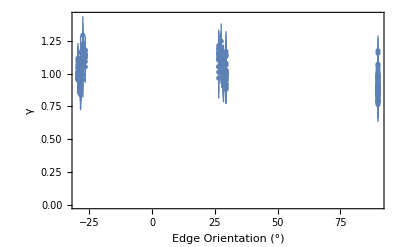

```mathematica
(* EXAMPLE: explore whether there is any correlation of an edge's tension with its orientation *)
(* we can use the chord-based unit vectors as a measure of each edge's orientation *)
θListDegrees=(If[#[[1]]!=0,ArcTan[#[[2]]/#[[1]]],N[π/2]]/Degree)&/@edgeListForCellFITRagged[[All,4,1]];
γVsθList=Transpose[{θListDegrees,γWithStError}]; (* this will automatically include the error bars *)
ListPlot[γVsθList,PlotRange->Automatic, Frame->{{True,False},{True,False}}, FrameLabel->{"Edge Orientation (°)","γ"}]
```

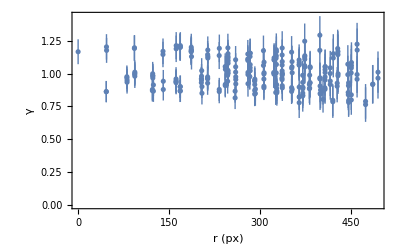

```mathematica
(* EXAMPLE: explore whether there is any correlation of an edge's tension with distance from the center of the image (wound center) *)
rList=EuclideanDistance[Mean[#],{w/2,h/2}]&/@edgeListForCellFITRagged[[All,3]];
γVsRList=Transpose[{rList,γWithStError}]; (* this will automatically include the error bars *)
ListPlot[γVsRList,PlotRange->Automatic, Frame->{{True,False},{True,False}}, FrameLabel->{"r (px)","γ"}]
```

{{50,60},{60,70},{70,80},{80,90},{90,100},{100,110},{110,120},{120,130},{130,140},{140,150}}

StandardDeviation::shlen: The argument {} should have at least two elements.

General::stop: Further output of StandardDeviation::shlen will be suppressed during this calculation.

{{0.274725 Mean[{}]0.274725 StandardDeviation[{}],Mean[{}]StandardDeviation[{}]},{0.274725 Mean[{}]0.274725 StandardDeviation[{}],Mean[{}]StandardDeviation[{}]},{0.274725 Mean[{}]0.274725 StandardDeviation[{}],Mean[{}]StandardDeviation[{}]},{22.190.05,0.9560.019},{25.670.09,1.060.10},{0.274725 Mean[{}]0.274725 StandardDeviation[{}],Mean[{}]StandardDeviation[{}]},{0.274725 Mean[{}]0.274725 StandardDeviation[{}],Mean[{}]StandardDeviation[{}]},{33.900.17,0.930.06},{0.274725 Mean[{}]0.274725 StandardDeviation[{}],Mean[{}]StandardDeviation[{}]},{38.570.08,1.030.15}}

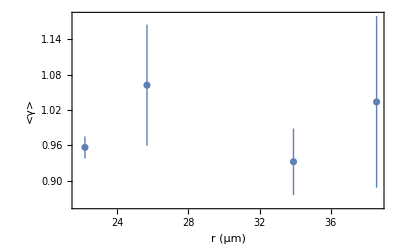

```mathematica
(* or bin the data to see how distribution varies with distance from *)
b1=50;
Δr=10;
binRanges =Table[{b1+Δr*(i-1),b1+Δr*(i)},{i,10}]
μmPerPixel=N[50/(986-804)]; (* need to double-check that this is correct *)
γVsRListBinned=Table[Select[γVsRList,binRanges[[i,1]]<=#[[1]]<binRanges[[i,2]]&],{i,10}];
γVsRListBinnedMeans={Around[μmPerPixel*Mean[#[[All,1]]],μmPerPixel*StandardDeviation[#[[All,1]]]],Around[Mean[#[[All,2,1]]],StandardDeviation[#[[All,2,1]]]]}&/@γVsRListBinned
ListPlot[Select[γVsRListBinnedMeans,NumberQ[#[[1,1]]]&],PlotRange->Automatic, Frame->{{True,False},{True,False}}, FrameLabel->{"r (μm)","<γ>"}]
```

StandardDeviation::shlen: The argument {} should have at least two elements.

General::stop: Further output of StandardDeviation::shlen will be suppressed during this calculation.

{{0.274725 Mean[{}]0.274725 StandardDeviation[{}],Mean[{}]StandardDeviation[{}]},{0.274725 Mean[{}]0.274725 StandardDeviation[{}],Mean[{}]StandardDeviation[{}]},{0.274725 Mean[{}]0.274725 StandardDeviation[{}],Mean[{}]StandardDeviation[{}]},{0.274725 Mean[{}]0.274725 StandardDeviation[{}],Mean[{}]StandardDeviation[{}]},{25.640.09,1.090.12},{0.274725 Mean[{}]0.274725 StandardDeviation[{}],Mean[{}]StandardDeviation[{}]},{0.274725 Mean[{}]0.274725 StandardDeviation[{}],Mean[{}]StandardDeviation[{}]},{34.010.17,0.940.06},{0.274725 Mean[{}]0.274725 StandardDeviation[{}],Mean[{}]StandardDeviation[{}]},{38.570.08,1.030.15}}

StandardDeviation::shlen: The argument {} should have at least two elements.

General::stop: Further output of StandardDeviation::shlen will be suppressed during this calculation.

{{0.274725 Mean[{}]0.274725 StandardDeviation[{}],Mean[{}]StandardDeviation[{}]},{0.274725 Mean[{}]0.274725 StandardDeviation[{}],Mean[{}]StandardDeviation[{}]},{0.274725 Mean[{}]0.274725 StandardDeviation[{}],Mean[{}]StandardDeviation[{}]},{22.190.05,0.9560.019},{25.7420.004,1.0060.007},{0.274725 Mean[{}]0.274725 StandardDeviation[{}],Mean[{}]StandardDeviation[{}]},{0.274725 Mean[{}]0.274725 StandardDeviation[{}],Mean[{}]StandardDeviation[{}]},{33.800.10,0.920.06},{0.274725 Mean[{}]0.274725 StandardDeviation[{}],Mean[{}]StandardDeviation[{}]},{0.274725 Mean[{}]0.274725 StandardDeviation[{}],Mean[{}]StandardDeviation[{}]}}

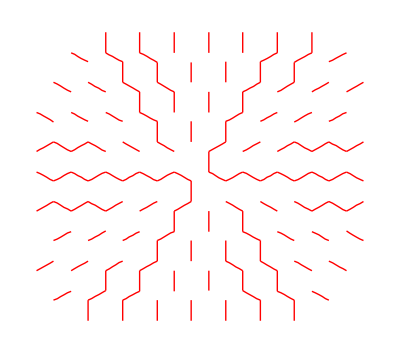

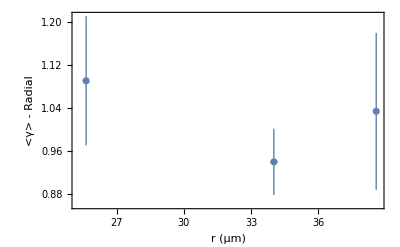

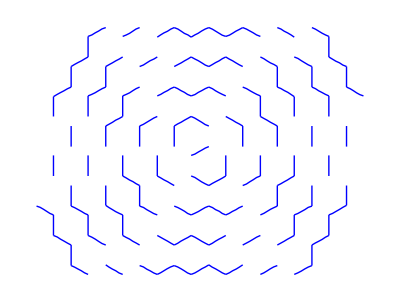

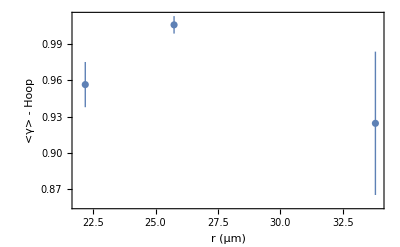

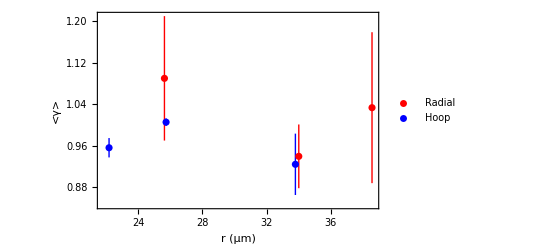

```mathematica
(* Can we do a similar analysis, but separating out the radial and hoop tensions? *)
radialDotProdList=((#[[-1]]-#[[1]])/EuclideanDistance[#[[-1]],#[[1]]]).((Mean[#]-{w/2,h/2})/EuclideanDistance[Mean[#],{w/2,h/2}])&/@edgeListForCellFITRagged[[All,3]];
edgesRadialBoolean=Abs[#]>Sqrt[2]/2&/@radialDotProdList;
edgesHoopBoolean=Abs[#]<Sqrt[2]/2&/@radialDotProdList;
b1=50;
Δr=10;
binRanges =Table[{b1+Δr*(i-1),b1+Δr*(i)},{i,10}];
μmPerPixel=N[50/(986-804)]; (* need to double-check that this is correct *)
γVsRListBinnedRadial=Table[Select[Pick[γVsRList,edgesRadialBoolean],binRanges[[i,1]]<=#[[1]]<binRanges[[i,2]]&],{i,10}];
γVsRListBinnedHoop=Table[Select[Pick[γVsRList,edgesHoopBoolean],binRanges[[i,1]]<=#[[1]]<binRanges[[i,2]]&],{i,10}];
γVsRListBinnedMeansRadial={Around[μmPerPixel*Mean[#[[All,1]]],μmPerPixel*StandardDeviation[#[[All,1]]]],Around[Mean[#[[All,2,1]]],StandardDeviation[#[[All,2,1]]]]}&/@γVsRListBinnedRadial
γVsRListBinnedMeansHoop={Around[μmPerPixel*Mean[#[[All,1]]],μmPerPixel*StandardDeviation[#[[All,1]]]],Around[Mean[#[[All,2,1]]],StandardDeviation[#[[All,2,1]]]]}&/@γVsRListBinnedHoop

Graphics[{Red,Line[#]&/@Pick[edgeListForCellFITRagged[[All,3]],edgesRadialBoolean]}]
ListPlot[Select[γVsRListBinnedMeansRadial,NumberQ[#[[1,2]]]&],PlotRange->Automatic, Frame->{{True,False},{True,False}}, FrameLabel->{"r (μm)","<γ> - Radial"}]
Graphics[{Blue,Line[#]&/@Pick[edgeListForCellFITRagged[[All,3]],edgesHoopBoolean]}]
ListPlot[Select[γVsRListBinnedMeansHoop,NumberQ[#[[1,2]]]&],PlotRange->Automatic, Frame->{{True,False},{True,False}}, FrameLabel->{"r (μm)","<γ> - Hoop"}]
ListPlot[{Select[γVsRListBinnedMeansRadial,NumberQ[#[[1,2]]]&],Select[γVsRListBinnedMeansHoop,NumberQ[#[[1,2]]]&]},PlotRange->Automatic, Frame->{{True,False},{True,False}}, FrameLabel->{"r (μm)","<γ>"},PlotStyle->{Red,Blue},PlotLegends->{"Radial","Hoop"}]
```

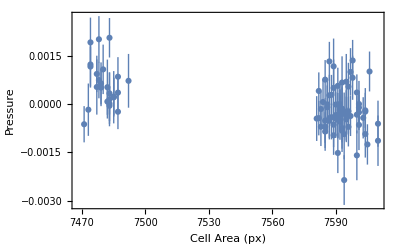

```mathematica
(* EXAMPLE: explore whether there is any correlation of a cell's pressure with its size *)
(* we can use the chord-based unit vectors as a measure of each edge's orientation *)
areaList=Area/@cellRegionList;
pVsAreaList=Transpose[{areaList,pWithStError}]; (* this will automatically include the error bars *)
ListPlot[pVsAreaList,PlotRange->Automatic, Frame->{{True,False},{True,False}}, FrameLabel->{"Cell Area (px)","Pressure"}]
```

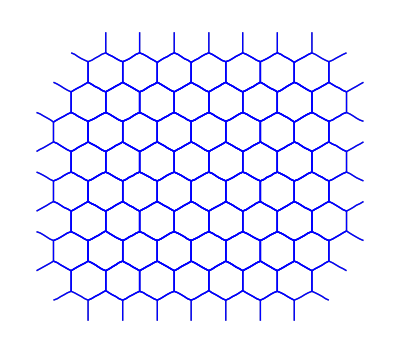

```mathematica
(* EXAMPLE: test compatibility with tension balance as described by Noll et al (2017) "Active tension network model suggests an exotic mechanical state realized in epithelial tissues" Nature Physics 13: 1221-1227. *)
verbose=False;
(* Define function for finding the two outside TJ angles for a given TJ of a chosen cell *)
(* if cell is ok, then calculate all the outer TJ angle pairs *)
angleMethod=3;
getTJAngles[edgeListForThisTJ_,cellID_,angleMethod_]:=(
(* angleMethod: 1 = chord; 2 = nearest segment; 3 = arc fit *)
edgeListForThisTJSorted=SortBy[edgeListForThisTJ,ArcTan[#[[angleMethod+3,1,1]],#[[angleMethod+3,1,2]]] &];
iOutside=First[First[Position[MemberQ[#[[1]],cellID]&/@edgeListForThisTJSorted,False]]];
edgeListForThisTJSorted=Reverse[RotateRight[edgeListForThisTJSorted,2-iOutside]];
If[verbose,Print[MemberQ[#[[1]],cellID]&/@edgeListForThisTJSorted]];
θListForThisTJ=ArcTan[#[[angleMethod+3,1,1]],#[[angleMethod+3,1,2]]]&/@edgeListForThisTJSorted;
If[verbose,Print[θListForThisTJ/Degree]];
θβ=Mod[θListForThisTJ[[1]]-θListForThisTJ[[2]],π];
θγ=Mod[θListForThisTJ[[2]]-θListForThisTJ[[3]],π];
{θβ,θγ}
)

outerTJAngleList={};
χList={};
Monitor[
Do[
cellID=includedCellIDs[[i]];
(* Gather all the edgeList entries adjacent to a single chosen cell; and check to make sure cell has all triple-junctions and is in interior of cell patch *)
edgeListForThisCell=Select[edgeListForCellFITRagged,MemberQ[#[[2,1]],cellID]||MemberQ[#[[2,2]],cellID]&];
tripleJunctionSetsForThisCell=DeleteDuplicates[Select[Flatten[edgeListForThisCell[[All,2]],1],MemberQ[#,cellID]&]];
allTripleJunctionQ=AllTrue[tripleJunctionSetsForThisCell,Length[#]==3&];
borderingExcludedCellIDs=Intersection[Flatten[tripleJunctionSetsForThisCell],excludedCellIDs];
interiorCellQ=Length[borderingExcludedCellIDs]==0;
If[!interiorCellQ&&verbose,Print["Cell ",cellID," has a border with one or more excluded cells: ",borderingExcludedCellIDs],If[!allTripleJunctionQ&&verbose,Print["Cell ",cellID," has one or more non-triple-junctions"]]];
nTJs=Length[tripleJunctionSetsForThisCell];
edgeListForThisCellByTJ=Table[Join[
Select[edgeListForThisCell,#[[2,1]]==tripleJunctionSetsForThisCell[[i]]&],
{#[[1]],Reverse[#[[2]]],Reverse[#[[3]]],Reverse[#[[4]]],Reverse[#[[5]]],Append[Reverse[#[[6,;;2]]],#[[6,3]]]}&/@Select[edgeListForThisCell,#[[2,2]]==tripleJunctionSetsForThisCell[[i]]&]
],{i,nTJs}];
edgeListForThisTJ=edgeListForThisCellByTJ[[1]];

If[interiorCellQ&&allTripleJunctionQ,(
TJAnglePairListForThisCell=getTJAngles[#,cellID,angleMethod]&/@edgeListForThisCellByTJ;
If[verbose,Print["Chosen cell has ",nTJs," triple-junctions"]];
If[verbose,Print["outer TJ angles for this cell: ",TJAnglePairListForThisCell/Degree]];
ratioList=((Sin[#[[2]]]/Sin[#[[1]]])&/@TJAnglePairListForThisCell);
If[verbose,Print["ratio list = ",ratioList]];
χThisCell=Times@@((Sin[#[[2]]]/Sin[#[[1]]])&/@TJAnglePairListForThisCell);
If[verbose,Print["χ = ",χThisCell]];
AppendTo[outerTJAngleList,{cellID,TJAnglePairListForThisCell}];
AppendTo[χList,{cellID,χThisCell}];
)]
,{i,Length[includedCellIDs]}]
,"Finding TJ angles for cell "<>ToString[i]<>" of "<>ToString[Length[includedCellIDs]]]
outerTJAngleList;
χList;
edgeListForAnalyzedCells=Flatten[Table[Select[edgeListForCellFITRagged,MemberQ[#[[2,1]],cellID]||MemberQ[#[[2,2]],cellID]&],{cellID,outerTJAngleList[[All,1]]}],1];
Graphics[{Gray,Line[#[[3]]]&/@edgeListForCellFITRagged,Blue,Line[#[[3]]]&/@edgeListForAnalyzedCells}]
```

Compare actual distribution of χ (blue) to control randomized distribution (red)

/Users/hutsonms/Library/CloudStorage/Box-Box/Research Sync/Mathematica Notebook Development/CreateMesh_UniformPressure_Outlines_2024.tif

Angles estimated using arc-fit method.

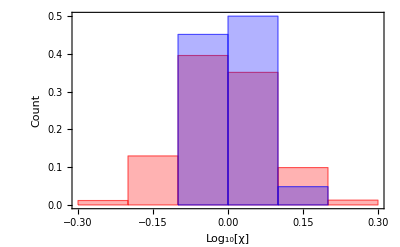

Actual Logχ distribution's mean +/- st.dev. = 0.00553665 +/- 0.0475607

Control Logχ distribution's mean +/- st.dev. = -0.00753465 +/- 0.0874205

Kolmogorov-Smirnov test of null hypothesis that data come from same distribution, p = 0.0000272133

(by comparison, Kolmogorov-Smirnov test of null hypothesis that two randomly generated controls come from same distribution, p = 0.495755)

```mathematica
outerTJAngleListFlattened=Flatten[outerTJAngleList[[All,2]]];
(* outerTJAngleListRandomized={#[[1]],Table[{RandomChoice[outerTJAngleListFlattened],RandomChoice[outerTJAngleListFlattened]},{i,Length[#[[2]]]}]}&/@outerTJAngleList; *)
outerTJAngleListSampled=RandomChoice[outerTJAngleList,10*nCells];
outerTJAngleListSampled2=RandomChoice[outerTJAngleList,10*nCells];
outerTJAngleListRandomized={#[[1]],Table[{θext1,#[[2,i,1]]+#[[2,i,2]]-θext1}/.θext1->RandomChoice[outerTJAngleListFlattened],{i,Length[#[[2]]]}]}&/@outerTJAngleListSampled;
outerTJAngleListRandomized2={#[[1]],Table[{θext1,#[[2,i,1]]+#[[2,i,2]]-θext1}/.θext1->RandomChoice[outerTJAngleListFlattened],{i,Length[#[[2]]]}]}&/@outerTJAngleListSampled2;
χListRandomized=Table[{outerTJAngleListRandomized[[i,1]],Times@@((Sin[#[[2]]]/Sin[#[[1]]])&/@outerTJAngleListRandomized[[i,2]])},{i,Length[outerTJAngleListRandomized]}];
χListRandomized2=Table[{outerTJAngleListRandomized2[[i,1]],Times@@((Sin[#[[2]]]/Sin[#[[1]]])&/@outerTJAngleListRandomized2[[i,2]])},{i,Length[outerTJAngleListRandomized2]}];
LogχList=Select[DeleteCases[Log10/@χList[[All,2]],Infinity|Indeterminate|ComplexInfinity],Im[#]==0&];
LogχListRandomized=Select[DeleteCases[Log10/@χListRandomized[[All,2]],Infinity|Indeterminate|ComplexInfinity],Im[#]==0&];
LogχListRandomized2=Select[DeleteCases[Log10/@χListRandomized2[[All,2]],Infinity|Indeterminate|ComplexInfinity],Im[#]==0&];
Print["Compare actual distribution of χ (blue) to control randomized distribution (red)"]
Print[segmentFilename]
Print["Angles estimated using ",Switch[angleMethod,1,"chord",2,"nearest-segment",3,"arc-fit"]," method."]
Show[
Histogram[LogχListRandomized,{0.1},"Probability",Frame->{{True,False},{True,False}},FrameLabel->{"Log_10[χ]","Count"},ChartStyle->Directive[Red,Opacity[0.3]]],
Histogram[LogχList,{0.1},"Probability",Frame->{{True,False},{True,False}},FrameLabel->{"Log_10[χ]","Count"},ChartStyle->Directive[Blue,Opacity[0.3]]]
]
LogχMean=Mean[LogχList];
LogχStDev=StandardDeviation[LogχList];
LogχControlMean=Mean[LogχListRandomized];
LogχControlStDev=StandardDeviation[LogχListRandomized];
pValue=KolmogorovSmirnovTest[LogχList,LogχListRandomized];
Print["Actual Logχ distribution's mean +/- st.dev. = ",LogχMean," +/- ",LogχStDev]
Print["Control Logχ distribution's mean +/- st.dev. = ",LogχControlMean," +/- ",LogχControlStDev]
Print["Kolmogorov-Smirnov test of null hypothesis that data come from same distribution, p = ",pValue]
pValueForNullTest=KolmogorovSmirnovTest[LogχListRandomized,LogχListRandomized2];
Print["(by comparison, Kolmogorov-Smirnov test of null hypothesis that two randomly generated controls come from same distribution, p = ",pValueForNullTest,")"]
```

{1,5,4}

The three highest tension values are {1.220.16,1.250.13,1.290.15}

Black dot marks edge with high tension (1.220.16)

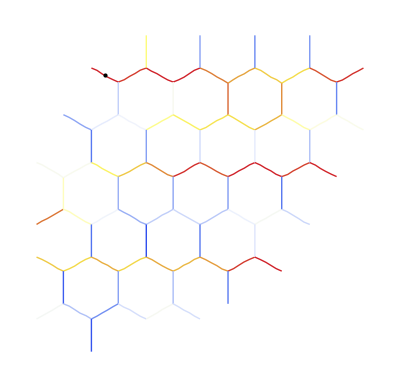

Black dot marks edge with high tension (1.250.13)

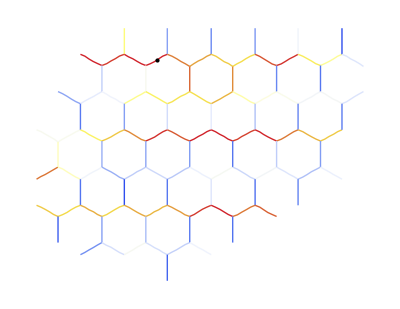

Black dot marks edge with high tension (1.290.15)

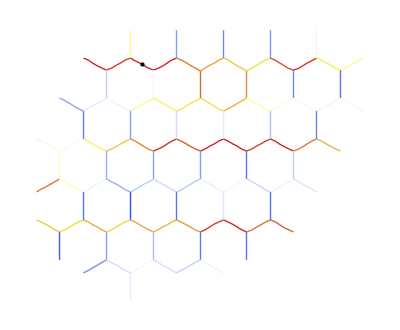

```mathematica
(* EXAMPLE: take a closer look at the regions around the highest few tension values *)
highestγIndices=Ordering[γWithStError][[-3;;]]
Print["The three highest tension values are ",γWithStError[[highestγIndices]] ]
(* get the mean position of the edges corresponding to these high γ values *)
posList = Mean/@edgeListForCellFITRagged[[highestγIndices,3]];
(* make a color-coded plot of all edges that have coordinates lying within a given distance of these positions *)
cutoff =6*medianEdgeLength;
nearbyBooleanList = (Min[(EuclideanDistance[#,posList[[1]]]&/@#)]<=cutoff)&/@edgeListForCellFITRagged[[All,3]];
Print["Black dot marks edge with high tension (",γWithStError[[highestγIndices[[1]]]] ,")"]
localγMap=Graphics[{
Pick[Table[{γColorList[[i]],Line[edgeListForCellFITRagged[[i,3]]]},{i,nγ}],nearbyBooleanList],
Black,Point[posList[[1]]]
}]
nearbyBooleanList = (Min[(EuclideanDistance[#,posList[[2]]]&/@#)]<=cutoff)&/@edgeListForCellFITRagged[[All,3]];
Print["Black dot marks edge with high tension (",γWithStError[[highestγIndices[[2]]]] ,")"]
localγMap=Graphics[{
Pick[Table[{γColorList[[i]],Line[edgeListForCellFITRagged[[i,3]]]},{i,nγ}],nearbyBooleanList],
Black,Point[posList[[2]]]
}]
nearbyBooleanList = (Min[(EuclideanDistance[#,posList[[3]]]&/@#)]<=cutoff)&/@edgeListForCellFITRagged[[All,3]];
Print["Black dot marks edge with high tension (",γWithStError[[highestγIndices[[3]]]] ,")"]
localγMap=Graphics[{
Pick[Table[{γColorList[[i]],Line[edgeListForCellFITRagged[[i,3]]]},{i,nγ}],nearbyBooleanList],
Black,Point[posList[[3]]]
}]
```

Assemble information about the geometry and the inferred tensions and pressures into a format that can be saved to an .xlsx file. This information could later be loaded into Mathematica or other programs for further analysis or to be combined with analysis of other images. The saved .xlsx file should have 5 worksheets with the following information:

Edge Data: 	edgeID	adjCellID1	adjCellID2	Jct1-cellID List (up to 4 cellIDs)	Jct2-cellID List (up to 4 cellIDs)	List of node coordinates
Tangent Vectors and Curvature:	edgeID	chord_vec1	chord_vec2	nearestSeg_vec1	nearestSeg_vec2	arcFit_vec1	arcFit_vec2	arcFit_curvature
Tensions:		edgeID	tension	standard error
Cell Data:		indexInList	cellID	centroid_x	centroid_y	ordered list of edgeIDs
Pressures:	indexInList	cellID	pressure		standard error

```mathematica
(* First gather the information needed for the Edge Data worksheet *)
maxNodes=Max[Length[#[[3]]]&/@edgeListForCellFITRagged];
edgeDataHeaders=Join[{"edgeID","adjCellID1","adjCellID2","Jct1-cellID1","Jct1-cellID2","Jct1-cellID3","Jct1-cellID4","Jct2-cellID1","Jct2-cellID2","Jct2-cellID3","Jct2-cellID4"},Flatten[Table[{"x_"<>IntegerString[j,10,2],"y_"<>IntegerString[j,10,2]},{j,maxNodes}]]];
edgeData=Prepend[Table[Flatten[{i,edgeListForCellFITRagged[[i,1]],PadRight[#,4,""]&/@edgeListForCellFITRagged[[i,2]],edgeListForCellFITRagged[[i,3]]}],{i,Length[edgeListForCellFITRagged]}],edgeDataHeaders];
Print["What the first 10 rows of the Edge Data worksheet should look like ..."]
TableForm[edgeData[[;;10]]]
(* Then gather the information needed for the Tangent Vectors and Curvatures worksheet *)
tangentVectorsHeaders=Flatten[{"edgeID",{"vec1x_"<>#,"vec1y_"<>#,"vec2x_"<>#,"vec2y_"<>#}&/@{"chord","nearSeg","arcFit"},"curvature_arcFit"}]
tangentVectorsData=Prepend[Table[Flatten[{i,edgeListForCellFITRagged[[i,4;;]]}],{i,Length[edgeListForCellFITRagged]}],tangentVectorsHeaders];
Print["What the first 10 rows of the Tangent Vectors and Curvature worksheet should look like ..."]
TableForm[tangentVectorsData[[;;10]]]
(* Then gather the information needed for the Tensions worksheet *)
tensionHeaders={"edgeID","tension","st_error"}
tensionData=Prepend[Table[Flatten[{i,γWithStError[[i,1]],γWithStError[[i,2]]}],{i,Length[edgeListForCellFITRagged]}],tensionHeaders];
Print["What the first 10 rows of the Tensions worksheet should look like ..."]
TableForm[tensionData[[;;10]]]
```

What the first 10 rows of the Edge Data worksheet should look like ...

edgeID | adjCellID1 | adjCellID2 | Jct1-cellID1 | Jct1-cellID2 | Jct1-cellID3 | Jct1-cellID4 | Jct2-cellID1 | Jct2-cellID2 | Jct2-cellID3 | Jct2-cellID4 | x_01 | y_01 | x_02 | y_02 | x_03 | y_03 | x_04 | y_04 | x_05 | y_05 | x_06 | y_06
1 | 655 | 7864 | 0 | 655 | 7864 |  | 655 | 7864 | 8520 |  | 162. | 848. | 171.593 | 844. | 180.204 | 838. | 189.137 | 832.727 | 198.698 | 828.151 | 208. | 824.
2 | 655 | 8520 | 655 | 7864 | 8520 |  | 655 | 1311 | 8520 |  | 208. | 824. | 218.298 | 828. | 227.428 | 833.714 | 236.847 | 838.694 | 245.647 | 844.294 | 256. | 848.
3 | 655 | 1311 | 655 | 1311 | 8520 |  | 655 | 1311 | 6554 |  | 256. | 848. | 256. | 862. | 256. | 876. | 256. | 890. | 256. | 904. |  | 
4 | 1311 | 8520 | 655 | 1311 | 8520 |  | 1311 | 8520 | 9175 |  | 256. | 848. | 264.598 | 842.803 | 274.288 | 838.356 | 283.501 | 832.749 | 292.592 | 827.704 | 302. | 824.
5 | 1311 | 9175 | 1311 | 8520 | 9175 |  | 1311 | 1966 | 9175 |  | 302. | 824. | 311.371 | 827.741 | 320.604 | 832.302 | 329.484 | 838.242 | 338.153 | 844. | 348. | 848.
6 | 1311 | 1966 | 1311 | 1966 | 9175 |  | 1311 | 1966 | 6554 |  | 348. | 848. | 348. | 862. | 348. | 876. | 348. | 890. | 348. | 904. |  | 
7 | 1966 | 9175 | 1311 | 1966 | 9175 |  | 1966 | 9175 | 9830 |  | 348. | 848. | 358.26 | 843.87 | 368.203 | 838.398 | 377.179 | 832.642 | 386.618 | 827.691 | 396. | 822.
8 | 1966 | 9830 | 1966 | 9175 | 9830 |  | 1966 | 2621 | 9830 |  | 396. | 822. | 404.828 | 827.914 | 413.761 | 833.381 | 423.658 | 838. | 432.522 | 843.761 | 442. | 848.
9 | 1966 | 2621 | 1966 | 2621 | 9830 |  | 1966 | 2621 | 6554 |  | 442. | 848. | 442. | 862. | 442. | 876. | 442. | 890. | 442. | 904. |  |

{edgeID,vec1x_chord,vec1y_chord,vec2x_chord,vec2y_chord,vec1x_nearSeg,vec1y_nearSeg,vec2x_nearSeg,vec2y_nearSeg,vec1x_arcFit,vec1y_arcFit,vec2x_arcFit,vec2y_arcFit,curvature_arcFit}

What the first 10 rows of the Tangent Vectors and Curvature worksheet should look like ...

edgeID | vec1x_chord | vec1y_chord | vec2x_chord | vec2y_chord | vec1x_nearSeg | vec1y_nearSeg | vec2x_nearSeg | vec2y_nearSeg | vec1x_arcFit | vec1y_arcFit | vec2x_arcFit | vec2y_arcFit | curvature_arcFit
1 | 0.886585 | -0.462566 | -0.886585 | 0.462566 | 0.922971 | -0.384869 | -0.913199 | 0.407515 | 0.869902 | -0.493225 | -0.902188 | 0.431343 | 0.00134607
2 | 0.894427 | 0.447214 | -0.894427 | -0.447214 | 0.932152 | 0.362066 | -0.941507 | -0.336994 | 0.88923 | 0.457459 | -0.899506 | -0.436909 | -0.000428168
3 | 0. | 1. | 0. | -1. | 0. | 1. | 0. | -1. | 0. | 1. | 0. | -1. | 0.
4 | 0.886585 | -0.462566 | -0.886585 | 0.462566 | 0.855834 | -0.51725 | -0.930483 | 0.366336 | 0.859113 | -0.511785 | -0.911239 | 0.411877 | 0.00217537
5 | 0.886585 | 0.462566 | -0.886585 | -0.462566 | 0.928718 | 0.370786 | -0.926481 | -0.376342 | 0.902834 | 0.42999 | -0.869161 | -0.494529 | 0.00140397
6 | 0. | 1. | 0. | -1. | 0. | 1. | 0. | -1. | 0. | 1. | 0. | -1. | 0.
7 | 0.879292 | -0.476283 | -0.879292 | 0.476283 | 0.927664 | -0.373417 | -0.854999 | 0.518629 | 0.91166 | -0.410944 | -0.842248 | 0.53909 | -0.00267681
8 | 0.870563 | 0.492057 | -0.870563 | -0.492057 | 0.830801 | 0.556569 | -0.91286 | -0.408272 | 0.832312 | 0.554307 | -0.904166 | -0.427181 | -0.00277101
9 | 0. | 1. | 0. | -1. | 0. | 1. | 0. | -1. | 0. | 1. | 0. | -1. | 0.

{edgeID,tension,st_error}

What the first 10 rows of the Tensions worksheet should look like ...

tensionsHeaders |  | 
1 | 1.22353 | 0.162325
2 | 1.19035 | 0.143595
3 | 1.07107 | 0.144868
4 | 1.29178 | 0.145256
5 | 1.24611 | 0.134619
6 | 0.904955 | 0.123913
7 | 1.16287 | 0.12222
8 | 1.14127 | 0.11751
9 | 0.884005 | 0.119302

64

Visualization that the cellRegion (blue) matches the nodes extracted from edgeListForCellFITRagged (red)

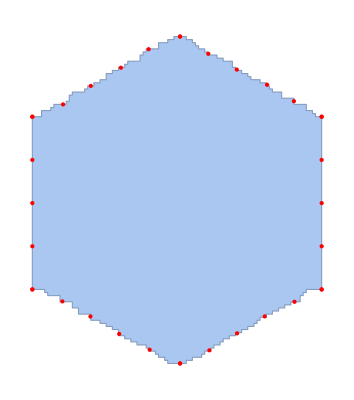

What the first 10 rows of the Cell Data worksheet should look like ...

cellIndex | cellID | x_centroid | y_centroid | edgeID01 | edgeID02 | edgeID03 | edgeID04 | edgeID05 | edgeID06
1 | 655 | 208.767 | 876.225 | 1 | 2 | 3 |  |  | 
2 | 1311 | 301.955 | 876.195 | 3 | 4 | 5 | 6 |  | 
3 | 1966 | 395.083 | 876.181 | 6 | 7 | 8 | 9 |  | 
4 | 2621 | 488.857 | 876.11 | 9 | 10 | 11 | 12 |  | 
5 | 3277 | 582.036 | 876.195 | 12 | 13 | 14 | 15 |  | 
6 | 3932 | 675.177 | 876.201 | 15 | 16 | 17 | 18 |  | 
7 | 4587 | 769. | 876.173 | 18 | 19 | 20 | 21 |  | 
8 | 5243 | 862.83 | 876.158 | 21 | 22 | 23 |  |  | 
9 | 7864 | 161.216 | 795.254 | 1 | 24 | 25 | 26 |  |

{cellIndex,cellID,pressure,st_error}

What the first 10 rows of the Pressures worksheet should look like ...

cellIndex | cellID | pressure | st_error
1 | 655 | 0.00116942 | 0.000862367
2 | 1311 | 0.00191413 | 0.000768528
3 | 1966 | -0.000238274 | 0.000730867
4 | 2621 | -3.20695×10^-7 | 0.000716181
5 | 3277 | 0.00200978 | 0.000719052
6 | 3932 | 0.000994905 | 0.000739592
7 | 4587 | -0.0006504 | 0.000783288
8 | 5243 | 0.000498599 | 0.000881691
9 | 7864 | -0.000357432 | 0.000782467

```mathematica
(* Then gather the information needed for the Cell Data worksheet *)
centroidList=RegionCentroid/@cellRegionList;
Monitor[edgeDataForSelectedCell=Table[Select[edgeListForCellFITRagged,MemberQ[#[[1]],includedCellIDs[[i]]]&],{i,Length[includedCellIDs]}];,"Finding matching edges for cell #"<>ToString[i]<>" of "<>ToString[Length[includedCellIDs]]]
Monitor[edgeIDsForSelectedCell=Table[Flatten[Position[edgeListForCellFITRagged[[All,1]],#]&/@edgeDataForSelectedCell[[i,All,1]]],{i,Length[includedCellIDs]}];,"Gathering edgeIDs for cell #"<>ToString[i]<>" of "<>ToString[Length[includedCellIDs]]]
i=RandomInteger[Length[cellRegionList]]
Print["Visualization that the cellRegion (blue) matches the nodes extracted from edgeListForCellFITRagged (red)"]
Show[cellRegionList[[i]],Graphics[{Red, Point/@Flatten[edgeDataForSelectedCell[[i,All,3]],1]}]]
maxEdges=Max[Length/@edgeIDsForSelectedCell];
cellDataHeaders=Flatten[{"cellIndex","cellID","x_centroid","y_centroid",Table["edgeID"<>IntegerString[j,10,2],{j,maxEdges}]}];
cellData=Prepend[Table[Flatten[{i,includedCellIDs[[i]],centroidList[[i]],edgeIDsForSelectedCell[[i]]}],{i,Length[includedCellIDs]}],cellDataHeaders]; 
Print["What the first 10 rows of the Cell Data worksheet should look like ..."]
TableForm[cellData[[;;10]]]
(* and finally gather the informatin needed for the Pressures worksheet *)
pressureHeaders={"cellIndex","cellID","pressure","st_error"}
pressureData=Prepend[Table[Flatten[{i,includedCellIDs[[i]],pWithStError[[i,1]],pWithStError[[i,2]]}],{i,Length[includedCellIDs]}],pressureHeaders];
Print["What the first 10 rows of the Pressures worksheet should look like ..."]
TableForm[pressureData[[;;10]]]
```

```mathematica
(* save information about the geometry and the inferred tensions and pressures *)
assembledData={edgeData,tangentVectorsData,tensionData,cellData,pressureData};
Export["cellFitResults_"<>(StringSplit[FileNameTake[segmentFilename],"."][[1]])<>".xlsx",assembledData]
```

cellFitResults_CreateMesh_UniformPressure_Outlines_2024.xlsx

```mathematica
endTime=AbsoluteTime[];
elaspedTime=endTime-startTime;
Print["Full notebook evaluation required ",elaspedTime," s or ",elaspedTime/60," min."]
```

Full notebook evaluation required 145.40097 s or 2.4233495 min.